# Evaluating Black-Box Physics Through Optical Emulation

## An illustrated computational essay, in twelve stages

Hubert Kołcz

Given only black-box access to a device — the settings that go in, the clicks that come out — under what conditions is it mathematically impossible to distinguish a genuinely quantum machine from an efficient classical optical emulation of it? This essay answers by building the certification out of two provably independent lenses: a correlation lens that classifies measurement statistics by graph invariants, and a geometric lens that prices resource scaling by a dynamical Lie algebra. The KCBS pentagon is the atom, and its exact hierarchy — classical 2 < quantum Sqrt[5] < exclusivity-only 5/2 — reappears at every stage; pentagon-mesh gluing supplies the composition algebra; analogue Hawking radiation supplies the application. The essay is built to be run: every number below is recomputed in this notebook's own kernel, and every stage carries at least one figure you can regenerate and drag. It proceeds start to finish — from the sealed box, through the smallest example and its one designed-in blind spot, the second lens that closes it, an optimal gluing pattern certified by ergodic optimization, and finally to two extensions the framework was not built for — ending on a single pentagon that catalyzes a clique of size 17 in a structure that would otherwise stay dormant. Established results are cited by number and used as tools; what follows is what they were used to build.

## The Instrument: Two Lenses and Four Kinds of Check

Everything below runs on one instrument, and it helps to see its shape before the story starts. Two lenses look at the box. The correlation lens draws a graph — measurements that can never both succeed are joined by an edge — and reads three invariants off it [1]. The geometric lens ignores the statistics entirely and instead counts how many independent motions a classical compiler would need to reproduce the device [2]. A box is safely classical-emulable only when both lenses agree; the interesting cases are exactly where one lens runs out of reach.

The checks themselves fall into four kinds, and it is worth keeping them straight, because only the first kind actually grades the device — the rest increasingly audit the measuring apparatus itself. This diagram is the map every later stage points back to:

The assessment instrument at a glance, colour-coded by what each check interrogates:

```mathematica
Module[{chip, cat, blue = RGBColor[0.20, 0.45, 0.85],
   green = RGBColor[0.30, 0.60, 0.35], amber = RGBColor[0.85, 0.55, 0.20],
   plum = RGBColor[0.62, 0.30, 0.55]},
 chip = Function[{t, c}, Framed[Style[t, 9, White, FontFamily -> "Helvetica"],
    Background -> c, FrameStyle -> White, RoundingRadius -> 4,
    ImageSize -> {172, 26}, Alignment -> Center]];
 cat = Function[{title, sub, chips, c}, Framed[Column[
     Prepend[chips, Column[{Style[title, Bold, 10, c],
        Style[sub, Italic, 8, GrayLevel[0.45]]}, Spacings -> 0.1]],
     Spacings -> 0.45, Alignment -> Center], FrameStyle -> c,
    RoundingRadius -> 8, Background -> Lighter[c, 0.9], ImageMargins -> 3]];
 Grid[{{
    cat["1 • DEVICE METRICS", "compare data → fixed boundary",
     {chip["C1 no-disturbance", blue], chip["C2 contextual fraction", blue],
      chip["C3 CE^2 clique load", blue], chip["C4 possibilistic support", blue],
      chip["C5 node sum vs 2, √5, 5/2", blue]}, blue],
    cat["2 • SELF-VALIDATION", "checks the tool, not a device",
     {chip["sanity anchors", green], chip["A1–A5 blueprint audit", green]}, green],
    cat["3 • TRUST / SCOPE", "what the engine cannot see",
     {chip["G7 DLA hook (white-box)", amber],
      chip["η* = 2/√5 reach theorem", amber]}, amber],
    cat["4 • ACCESS EXPANSION", "re-engineer the measurement",
     {chip["G8 attenuation (OQ2)", plum], chip["G9 antibunching g^2(0)", plum],
      chip["OQ1 interventional DLA", plum]}, plum]
   }}, Spacings -> {0.6, 0}, Alignment -> Top]]
```

1 • DEVICE METRICS
compare data → fixed boundary
C1 no-disturbance
C2 contextual fraction
C3 CE^2 clique load
C4 possibilistic support
C5 node sum vs 2, √5, 5/2 | 2 • SELF-VALIDATION
checks the tool, not a device
sanity anchors
A1–A5 blueprint audit | 3 • TRUST / SCOPE
what the engine cannot see
G7 DLA hook (white-box)
η* = 2/√5 reach theorem | 4 • ACCESS EXPANSION
re-engineer the measurement
G8 attenuation (OQ2)
G9 antibunching g^2(0)
OQ1 interventional DLA

Category 1 is the only column that says anything about the device by thresholding its click data against a fixed boundary. Category 2 checks that the engine's own arithmetic is right before any device is sampled. Category 3 states, honestly, where the method provably cannot succeed no matter what data arrives — G7 reads a white-box declaration, and the detection efficiency η* = 2/Sqrt[5] is a hard floor below which statistics alone can never close the loophole. Category 4 does not add a new threshold at all; it re-engineers what gets measured. Keep this four-way split in view: several later stages are really about moving a question from one column to another.

The three-tier boundary every Category-1 check is calibrated against:

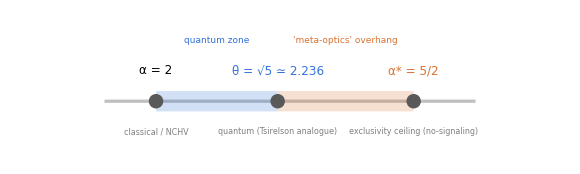

```mathematica
Module[{y0 = 0, a = 2, th = N[Sqrt[5]], as = 2.5},
 Graphics[{
   {GrayLevel[0.75], Thickness[0.004], Line[{{1.9, y0}, {2.62, y0}}]},
   {RGBColor[0.20, 0.45, 0.85, 0.22], Rectangle[{a, -0.05}, {th, 0.05}]},
   {RGBColor[0.85, 0.45, 0.20, 0.22], Rectangle[{th, -0.05}, {as, 0.05}]},
   {GrayLevel[0.35], PointSize[0.018], Point[{a, y0}], Point[{th, y0}], Point[{as, y0}]},
   Text[Style["α = 2", 12], {a, 0.15}],
   Text[Style["classical / NCHV", 8, GrayLevel[0.5]], {a, -0.15}],
   Text[Style["θ = √5 ≃ 2.236", 12, RGBColor[0.20, 0.45, 0.85]], {th, 0.15}],
   Text[Style["quantum (Tsirelson analogue)", 8, GrayLevel[0.5]], {th, -0.15}],
   Text[Style["α* = 5/2", 12, RGBColor[0.85, 0.45, 0.20]], {as, 0.15}],
   Text[Style["exclusivity ceiling (no-signaling)", 8, GrayLevel[0.5]], {as, -0.15}],
   Text[Style["quantum zone", 9, RGBColor[0.20, 0.45, 0.85]], {(a + th)/2, 0.30}],
   Text[Style["'meta-optics' overhang", 9, RGBColor[0.85, 0.45, 0.20]], {(th + as)/2, 0.30}]
   }, ImageSize -> 580, PlotRange -> {{1.8, 2.72}, {-0.28, 0.42}}, AspectRatio -> 0.30]]
```

Sqrt[5] is the pentagon's analogue of the Tsirelson bound: the most a genuine quantum device can score. 5/2 is its analogue of the no-signaling ceiling: the most reachable while still respecting no-disturbance. The strip between them — the 'meta-optics' overhang — is the adversary's room, and it is the territory this whole project is built to survey.

## Map of the Work — Objectives, Stages, and Verified Numbers

O1 correlation-based classification of statistics → Stages 1-2, 4 (GE-001, CF-001..004).
O2 Lie-algebraic resource scaling → Stages 5-6 (LP-002).
O3 conditions for indistinguishability → Stages 3-4 (BBT-002, BBT-004).
O4 Hawking illustration → The Cherry on Top (HK-003, HK-006, HK-007).
O5 signaling / communication feasibility → Stage 13 (SIG-001..003).
Priority: AB-sheaf derivation of the composed bound → Stage 12 (ESSAY-005, SH-006).
D1: GE copies vs θ(G) → Stages 10-11 (GE-002..004, ERG-003).
MESH: pentagon gluing → Stages 7-8 (MESH-001..009, CERT-001..002).
MBQC: cluster-state realization → Stage 9 (MESH-007..008, LP-003).

Results at a glance (every number kernel-verified in a module):
Classical 2 < quantum √5 = 2.2360679775 < NCHV 5/2 (GE-001); contextual fraction 2√5 - 4 = 0.4721.
Gluing limit densities: trans tau* = 1.3767177459, cis = 3/2; best word (cct)^inf gap 0.0698975 per block, beating pure-trans by 61%.
Epsilon-certificate ladder Gamma_7..Gamma_10 = 0.0770206, 0.0752664, 0.0720260, 0.0714575, bracketing gap(cct).
Catalysis: ω(C9^v3) = 8 proven; ω(C9 v C9 v C9 v C5) ≥ 17 (17-clique witness, family [1,3,5,5,3]).
Geometric lens: single so(3) generator DLA = 1 (leaf) vs full cascade DLA = 3 (sphere); CV Hawking generator DLA = 10 = sp(4,R), active.
Signaling: SF(C5, quantum) = 2√5 - 4 bits per round.

## Part I — The Atom and the Two-Lens Certificate

The central question, the KCBS-pentagon atom, and the two lenses that certify it: the correlation lens (the three-number ruler α, θ, α*) and the geometric lens (the dynamical Lie algebra), joined by the black-box protocol and its constructive mirror, the optical compiler. Modules: Stages 0-6. Objectives O1, O2, O3; tracks D2, BBT, EMU.

## Stage 0 — The Question: The Sealed Box

Imagine a sealed box with some inputs and outputs. It behaves in ways that look quantum: its outputs show correlations no ordinary classical device should be able to produce. Can you ever be completely certain it is genuinely quantum, just by watching what goes in and out, without opening it — or could a clever engineer build a purely classical fake that produces the exact same numbers? That is the founding question, and the honest starting picture has two possible interiors behind one identical stream of clicks.

A device you can only poke from outside: same clicks, two candidate interiors:

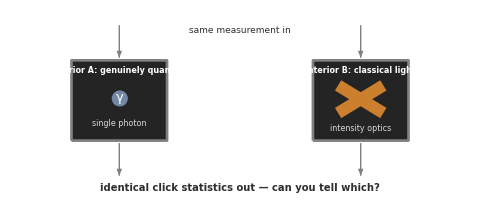

```mathematica
Module[{bx, navy = RGBColor[0.16, 0.28, 0.46], amber = RGBColor[0.80, 0.50, 0.18], ink = GrayLevel[0.18]},
 bx = Function[{x, lbl, guts}, {
    {GrayLevel[0.14], EdgeForm[{GrayLevel[0.5], Thickness[0.004]}],
     Rectangle[{x - 0.95, -0.8}, {x + 0.95, 0.8}]}, guts,
    White, Text[Style[lbl, 8, FontFamily -> "Helvetica", Bold], {x, 0.6}]}];
 Graphics[{
   bx[-2.4, "interior A: genuinely quantum",
    {Lighter[navy, 0.35], Disk[{-2.4, 0.05}, 0.16],
     White, Text[Style["γ", 13, FontFamily -> "Helvetica"], {-2.4, 0.05}],
     GrayLevel[0.85], Text[Style["single photon", 8, FontFamily -> "Helvetica"], {-2.4, -0.45}]}],
   bx[2.4, "interior B: classical light",
    {amber, Thickness[0.018],
     Line[{{1.95, 0.3}, {2.85, -0.25}}], Line[{{1.95, -0.25}, {2.85, 0.3}}],
     GrayLevel[0.85], Text[Style["intensity optics", 8, FontFamily -> "Helvetica"], {2.4, -0.55}]}],
   Arrowheads[0.03], GrayLevel[0.5],
   Arrow[{{-2.4, 1.5}, {-2.4, 0.85}}], Arrow[{{2.4, 1.5}, {2.4, 0.85}}],
   ink, Text[Style["same measurement in", 9, FontFamily -> "Helvetica"], {0, 1.4}],
   GrayLevel[0.5], Arrow[{{-2.4, -0.85}, {-2.4, -1.5}}], Arrow[{{2.4, -0.85}, {2.4, -1.5}}],
   ink, Text[Style["identical click statistics out — can you tell which?", 10, Bold, FontFamily -> "Helvetica"], {0, -1.75}]
   }, ImageSize -> 480, PlotRange -> {{-3.9, 3.9}, {-2.0, 1.6}}]
]
```

The rest of the essay is the sustained attempt to tell A from B — first with statistics, then, where statistics provably cannot, with geometry. To do that cleanly we need the simplest possible box where A and B already differ at all.

## Stage 1 — The Atom: the KCBS Pentagon

You do not want a complicated device to study this; you want the smallest one where 'quantum' and 'classical' already come apart. That object is the KCBS pentagon: five measurements arranged so each one is ever only compared with its two neighbours [3]. Joining mutually-exclusive measurements by an edge draws exactly a five-cycle.

The exclusivity graph of the five KCBS events is the five-cycle itself:

```mathematica
Labeled[
 Graph[CycleGraph[5],
  VertexLabels -> Thread[Range[5] -> (Style[#, GrayLevel[0.2], Bold, FontFamily -> "Helvetica", 12] & /@ {"P0", "P1", "P2", "P3", "P4"})],
  VertexSize -> Medium, VertexStyle -> RGBColor[0.16, 0.28, 0.46],
  EdgeStyle -> Directive[GrayLevel[0.72], Thickness[0.008]],
  GraphLayout -> "CircularEmbedding", ImageSize -> 250],
 Style["Each measurement excludes only its two neighbours", FontFamily -> "Helvetica", 10, GrayLevel[0.35]], Bottom]
```

```mathematica
□"Each measurement excludes only its two neighbours"
```

Why five, and not three or four? A triangle fails by Specker's obstruction: three mutually orthogonal directions in three dimensions form a single joint context, so classical equals quantum and there is no gap to exploit. Even cycles fail too — they admit a full noncontextual saturation. Odd, and at least five, is what is needed for the classical bound to strictly undershoot the quantum one. The pentagon is the smallest usable cycle: the hydrogen atom of contextuality. Watch where the quantum value sits, proportionally, as the cycle grows:

Drag n from 3 to 17: even cycles never open a gap, odd cycles ≥ 5 do — the right panel tracks the gap across every n:

```mathematica
Manipulate[
 Module[{a = Floor[n/2], th, as = n/2, navy = RGBColor[0.16, 0.28, 0.46],
    amber = RGBColor[0.80, 0.50, 0.18], gray = GrayLevel[0.6],
    gaps = {{3, 0.}, {4, 0.}, {5, 0.2361}, {6, 0.}, {7, 0.3177}, {8, 0.}, {9, 0.3601},
       {10, 0.}, {11, 0.3863}, {12, 0.}, {13, 0.4042}, {14, 0.}, {15, 0.4171}, {16, 0.}, {17, 0.4270}}},
  th = If[OddQ[n], N[n Cos[Pi/n]/(1 + Cos[Pi/n])], n/2];
  Row[{
    Graph[CycleGraph[n],
     VertexStyle -> If[OddQ[n] && n >= 5, navy, gray],
     EdgeStyle -> GrayLevel[0.7],
     VertexSize -> 0.3,
     GraphLayout -> "CircularEmbedding", ImageSize -> 160,
     PlotLabel -> Style["C" <> ToString[n], FontFamily -> "Helvetica", 12, GrayLevel[0.2]]],
    BarChart[{a, th, as}, ChartLabels -> Placed[Style[#, FontFamily -> "Helvetica", 9, GrayLevel[0.3]] & /@ {"classical", "quantum", "ceiling"}, Axis],
     ChartStyle -> {gray, navy, amber},
     PlotRange -> {0, n/2 + 0.6}, ImageSize -> 205, ImagePadding -> {{30, 8}, {34, 26}},
     LabelStyle -> Directive[FontFamily -> "Helvetica", 9, GrayLevel[0.3]],
     PlotLabel -> Style[Row[{"gap θ-α = ", NumberForm[th - a, {4, 3}]}], FontFamily -> "Helvetica", 10, GrayLevel[0.25]]],
    Show[
     ListPlot[gaps, Filling -> Axis, PlotStyle -> navy, FillingStyle -> Opacity[0.15, navy],
      PlotRange -> {{2.5, 17.5}, {-0.04, 0.5}}, AxesLabel -> {Style["n", FontFamily -> "Helvetica", 10], Style["gap", FontFamily -> "Helvetica", 10]},
      LabelStyle -> Directive[FontFamily -> "Helvetica", 9, GrayLevel[0.3]],
      ImageSize -> 235, ImagePadding -> {{34, 8}, {26, 16}}, GridLines -> Automatic,
      GridLinesStyle -> Directive[GrayLevel[0.9]]],
     Graphics[{amber, PointSize[0.035], Point[{n, th - a}]}]]
    }, Spacer[10]]],
 {{n, 5, "cycle size n  (3 to 17)"}, 3, 17, 1, Appearance -> "Labeled"},
 ControlPlacement -> Bottom]
```

The absolute gap θ-α grows slowly with n, but so does that ratio: proportionally, quantum sits closest to classical, and farthest from the supra-quantum ceiling, right at the pentagon. Five measurements is where the effect is cleanest to isolate, not where it is largest — which is exactly what you want in an atom. The same five directions also have a geometric picture worth making explorable: each measurement is a ray on a cone around a fixed axis, and exclusivity is precisely the statement that neighbouring rays are perpendicular.

Exclusivity as geometry — drag the cone's half-angle away from its one correct value and watch it break:

```mathematica
Manipulate[
 Module[{vv, dots, navy = RGBColor[0.16, 0.28, 0.46], amber = RGBColor[0.80, 0.50, 0.18],
    teal = RGBColor[0.24, 0.55, 0.50]},
  vv = Table[{Sin[th] Cos[4 Pi j/5], Sin[th] Sin[4 Pi j/5], Cos[th]}, {j, 0, 4}];
  dots = Table[vv[[j]] . vv[[Mod[j, 5] + 1]], {j, 1, 5}];
  Row[{
    Graphics3D[{
      {Opacity[0.14], teal, Cone[{{0, 0, -0.05}, {0, 0, 1.15}}, 1.15 Tan[th]]},
      {amber, Thick, Arrow[{{0, 0, 0}, {0, 0, 1.3}}]},
      Table[{navy, Arrow[{{0, 0, 0}, vv[[j]]}], GrayLevel[0.2],
         Text[Style[Subscript["v", j - 1], FontFamily -> "Helvetica", 11], 1.18 vv[[j]]]}, {j, 1, 5}],
      {Darker[teal, 0.3], Thick, Table[Line[{vv[[j]], vv[[Mod[j, 5] + 1]]}], {j, 1, 5}]}
      }, Boxed -> False, ImageSize -> 300, PlotRange -> 1.5, SphericalRegion -> True],
    BarChart[dots, PlotRange -> {-0.35, 1}, ChartStyle -> navy,
     ImageSize -> 260, ImagePadding -> {{32, 10}, {24, 28}},
     LabelStyle -> Directive[FontFamily -> "Helvetica", 10, GrayLevel[0.3]],
     PlotLabel -> Style["adjacent dot products (0 = perpendicular)", FontFamily -> "Helvetica", 10, GrayLevel[0.25]],
     GridLines -> {None, {0}}, GridLinesStyle -> Directive[amber, Dashed, AbsoluteThickness[1]]]
    }, Spacer[14]]],
 {{th, N[ArcCos[Sqrt[Cos[Pi/5]/(1 + Cos[Pi/5])]]], "cone half-angle"}, 0.4, 1.3, Appearance -> "Labeled"},
 ControlPlacement -> Bottom]
```

At the exact angle every adjacent pair is perpendicular — all five bars sit at zero — and the pentagon's fivefold symmetry forbids a partial failure, so moving the slider shifts them together. This is the object gate C5 is calibrated on. Its exact, algebraic invariants are what let every later stage run in certified arithmetic rather than by approximation.

## Stage 2 — The Correlation Lens: the Three-Number Ruler (2 < √5 < 5/2)

```mathematica
Import[FileNameJoin[{NotebookDirectory[], "figure-gallery", "figures", "hypergraph_paper.png"}]]
```

-Graphics-

Figure (Stage 2). Where √5 comes from: the two-copy GE exclusivity graph of the pentagon — 25 vertices (C5 x C5), 200 exclusivity edges, and exactly 10 maximal 5-cliques (pentads, drawn as translucent stars). Cabello's construction reaches √5 at two copies; here it is one object, its structure hard-gated 25 / 200 / 10 against the project's own count (GE-002, MESH-006).

For this pentagon three exact numbers matter. Two is the best any classical device can score. Sqrt[5] ≃ 2.236 is the best any genuine quantum device — a single photon — can score. And 5/2 is a theoretical ceiling that is mathematically possible under exclusivity alone but is not reachable by a real quantum particle. There is a quantum zone strictly between classical and this outer ceiling, and the gap Sqrt[5]-2 is the resource the whole project studies. The cleanest way to see all three at once is to read one pentagon three ways.

One pentagon, three readings of the same graph — the project's entire ruler on one line:

```mathematica
Module[{pts, pent},
 pts = Table[{Cos[Pi/2 + 2 Pi q/5], Sin[Pi/2 + 2 Pi q/5]}, {q, 0, 4}];
 pent = Function[{vals, cols, sVal, title, sub}, Labeled[
    Graphics[{
      {GrayLevel[0.65], Thickness[0.006], Line[Append[pts, First[pts]]]},
      Table[{cols[[q]], EdgeForm[GrayLevel[0.35]], Disk[pts[[q]], 0.2],
         If[MatchQ[cols[[q]], GrayLevel[_]], Black, White],
         Text[Style[vals[[q]], 10, Bold], pts[[q]]]}, {q, 1, 5}]},
     ImageSize -> 200, PlotRange -> 1.45, PlotRangePadding -> 0.12],
    Column[{Style[title, Bold, 10], Style[sub, Italic, 8, GrayLevel[0.45]],
       Style["S = " <> sVal, 13, Bold]}, Alignment -> Center, Spacings -> 0.25],
    Top]];
 Row[{
   pent[{"1", "0", "1", "0", "0"},
    {RGBColor[.2, .45, .85], GrayLevel[.82], RGBColor[.2, .45, .85], GrayLevel[.82], GrayLevel[.82]},
    "2", "CLASSICAL", "one possible world"],
   pent[{".45", ".45", ".45", ".45", ".45"},
    ConstantArray[RGBColor[.2, .45, .85], 5],
    "√5 ≃ 2.236", "QUANTUM", "geometry of cos^2"],
   pent[{".bd", ".bd", ".bd", ".bd", ".bd"},
    ConstantArray[RGBColor[.85, .55, .2], 5],
    "5/2", "EXCLUSIVITY ONLY", "Wright's one-half"]
   }, Spacer[8]]]
```

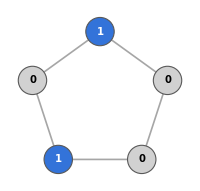
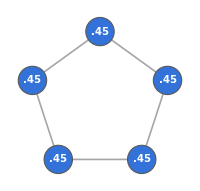
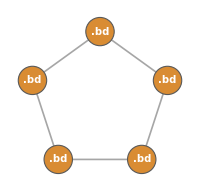

The same ruler, live — toggle the classical yes/no answers, tilt the quantum state β, and slide the five independent intensities, and watch each vertex's colour track its value against its own ceiling (2, √5, 5/2). Interactive board reused from the project's companion notebook TheBlackBoxGame.nb:

```mathematica
With[{c2 = Cos[Pi/5]/(1 + Cos[Pi/5])},
With[{vecs = Table[{Sqrt[1 - Cos[Pi/5]/(1 + Cos[Pi/5])] Cos[4 Pi i/5], Sqrt[1 - Cos[Pi/5]/(1 + Cos[Pi/5])] Sin[4 Pi i/5], Sqrt[Cos[Pi/5]/(1 + Cos[Pi/5])]}, {i, 0, 4}]},
With[{stateVec = Function[beta, {Sin[beta], 0, Cos[beta]}]},
With[{probsQ = Function[beta, Table[N[({Sin[beta], 0, Cos[beta]} . vecs[[i + 1]])^2], {i, 0, 4}]]},
With[{edgesP = {{0, 1}, {1, 2}, {2, 3}, {3, 4}, {4, 0}}},

Manipulate[
 Module[{selC, violC, scoreC, vcolC, ecolC, msgC, colC,
   p, totalQ, vcolQ,
   ivals, violI, totalI, vcolI, ecolI, msgI, colI,
   panelC, panelQ, panelI},

   selC = Flatten[Position[{b0, b1, b2, b3, b4}, True]] - 1;
   violC = Select[edgesP, MemberQ[selC, #[[1]]] && MemberQ[selC, #[[2]]] &];
   scoreC = Length[selC];
   {msgC, colC} = If[Length[violC] > 0,
     {"illegal", Red},
     {"score = " <> ToString[scoreC] <> " (ceiling 2)", If[scoreC <= 2, Darker[Green], Orange]}];
   vcolC = Table[i -> If[MemberQ[selC, i], Darker[Green], LightGray], {i, 0, 4}];
   ecolC = Table[UndirectedEdge[edgesP[[k, 1]], edgesP[[k, 2]]] ->
       If[MemberQ[violC, edgesP[[k]]], Red, Gray], {k, 5}];
   panelC = Column[{
      Graph[Range[0, 4], UndirectedEdge @@@ edgesP, VertexLabels -> "Name",
       VertexStyle -> vcolC, EdgeStyle -> ecolC, VertexSize -> 0.3,
       GraphLayout -> "CircularEmbedding", ImageSize -> 220,
       PlotLabel -> Style["classical", Bold]],
      Style[msgC, colC, Bold, 11]}];

   p = probsQ[beta]; totalQ = Total[p];
   vcolQ = Table[i -> Blend[{White, RGBColor[0.2, 0.45, 0.85]}, p[[i + 1]]], {i, 0, 4}];
   panelQ = Column[{
      Graph[Range[0, 4], UndirectedEdge @@@ edgesP, VertexLabels -> "Name",
       VertexStyle -> vcolQ, VertexSize -> 0.3, GraphLayout -> "CircularEmbedding",
       ImageSize -> 220, PlotLabel -> Style["quantum", Bold]],
      Style["score = " <> ToString[NumberForm[totalQ, 4]] <> " (max \[Sqrt]5 at \[Beta]=0)",
       Darker[Blue], Bold, 11]}];

   ivals = {i0, i1, i2, i3, i4};
   violI = Select[edgesP, (ivals[[#[[1]] + 1]] + ivals[[#[[2]] + 1]] > 1) &];
   totalI = Total[ivals];
   vcolI = Table[i -> Blend[{White, RGBColor[0.75, 0.2, 0.2]}, ivals[[i + 1]]], {i, 0, 4}];
   ecolI = Table[UndirectedEdge[edgesP[[k, 1]], edgesP[[k, 2]]] ->
       If[MemberQ[violI, edgesP[[k]]], Red, Gray], {k, 5}];
   {msgI, colI} = If[Length[violI] > 0,
     {"illegal", Red},
     {"score = " <> ToString[NumberForm[totalI, 3]] <> " (ceiling 5/2)",
      If[totalI <= 2.5 + 10^-9, Darker[Green], Orange]}];
   panelI = Column[{
      Graph[Range[0, 4], UndirectedEdge @@@ edgesP, VertexLabels -> "Name",
       VertexStyle -> vcolI, EdgeStyle -> ecolI, VertexSize -> 0.3,
       GraphLayout -> "CircularEmbedding", ImageSize -> 220,
       PlotLabel -> Style["classical light (non-classical)", Bold]],
      Style[msgI, colI, Bold, 11]}];

   Row[{panelC, panelQ, panelI}, Spacer[16]]
   ],
 Delimiter,
 Style["classical: pick yes/no answers", Bold],
 {{b0, False, "v0"}, {False, True}}, {{b1, False, "v1"}, {False, True}},
 {{b2, False, "v2"}, {False, True}}, {{b3, False, "v3"}, {False, True}},
 {{b4, False, "v4"}, {False, True}},
 Delimiter,
 Style["quantum: tilt the state", Bold],
 {{beta, 0, "state tilt \[Beta]"}, 0, 1.2},
 Delimiter,
 Style["classical light: set 5 independent intensities", Bold],
 {{i0, 0.5, "i0"}, 0, 1}, {{i1, 0.5, "i1"}, 0, 1}, {{i2, 0.5, "i2"}, 0, 1},
 {{i3, 0.5, "i3"}, 0, 1}, {{i4, 0.5, "i4"}, 0, 1}
 ]

]]]]]
```

The three panels are honestly different kinds of object, not three difficulty settings on the same game. The classical panel commits to a definite yes/no for each question in advance, capped at 2 by the pentagon's independence number. The quantum panel commits to nothing in advance; one state is measured five different ways, and its overlap with each measurement direction sets that question's own probability of 'yes' — all five equal, and summing to exactly Sqrt[5], only at the one symmetric state the slider starts on; tilt it and the total only ever falls, never rises. The classical-light panel is the odd one out: five independent intensities, free of any single consistent state, constrained only pairwise — exactly the fractional-packing relaxation of the classical panel's own rule, and exactly why it can reach higher, 5/2, without being quantum at all.

A third scoreboard — the contextual fraction. Slide the state parameter t and watch each pentagon vertex's colour intensity and the contextual fraction CF(t) = Max[0, 10 t − 4] move together. Reused from TheBlackBoxGame.nb:

```mathematica
cfBoard = Manipulate[
  Module[{cf, vcol, msg},
   cf = Max[0, 10 t - 4];
   vcol = Table[i -> Blend[{White, RGBColor[0.6, 0.2, 0.7]}, t/0.5], {i, 1, 5}];
   msg = "CF(t) = " <> ToString[NumberForm[cf, 4]] <>
     If[cf == 0, "  -- noncontextual (t <= 2/5)", "  -- a second, independent scoreboard from the θ-α gap"];
   Column[{
     Row[{
       Graph[CycleGraph[5], VertexLabels -> "Name", VertexStyle -> vcol, VertexSize -> 0.3,
        GraphLayout -> "CircularEmbedding", ImageSize -> 200, PlotLabel -> Style["t = " <> ToString[NumberForm[t, 3]], 10]],
       Spacer[15],
       Plot[Max[0, 10 x - 4], {x, 0.3, 0.5}, PlotRange -> {0, 1}, ImageSize -> 260,
        Epilog -> {PointSize[0.02], Darker[Purple], Point[{t, cf}]},
        AxesLabel -> {"t", "CF(t)"}, PlotLabel -> Style["contextual fraction, exact", 10]]
       }],
     Style[msg, Darker[Purple], Bold, 11]
     }]
   ],
  {{t, 0.4, "single-event probability t"}, 0.3, 0.5, 0.001}
  ]
```

In the classical reading no edge may join two TRUEs, so at most two of the five events fire and the sum caps at 2. In the quantum reading every event gets the same cos^2 weight from the Lovász umbrella, and the five add to exactly Sqrt[5]. In the exclusivity-only reading every pairwise-exclusive family sums to at most one, allowing one-half everywhere and a total of 5/2. Re-derive the triple directly, in exact arithmetic:

Cyclic orthogonality of the KCBS rays, and the three bounds, computed in-kernel:

```mathematica
c2 = Cos[Pi/5]/(1 + Cos[Pi/5]);
vecs = Table[{Sqrt[1 - c2] Cos[4 Pi i/5], Sqrt[1 - c2] Sin[4 Pi i/5], Sqrt[c2]}, {i, 0, 4}];
Column[{
  Row[{"adjacent orthogonality:   ",
    Table[Simplify[vecs[[i]] . vecs[[Mod[i, 5] + 1]]], {i, 1, 5}]}],
  Row[{"{α, θ, α*} = ", {2, Sqrt[5], 5/2},
    "   ≃   ", N[{2, Sqrt[5], 5/2}]}]
  }]
```

adjacent orthogonality:   {0,0,0,0,0}
{α, θ, α*} = {2,√5,5/2}   ≃   {2.,2.23607,2.5}

The orthogonality check returns {0,0,0,0,0} exactly, and θ = Sqrt[5] sits strictly between α = 2 and α* = 5/2. Gate C5 flags a device SUPRA-QUANTUM only when its node sum clears Sqrt[5]; the overhang from Sqrt[5] up to 5/2 is precisely the room a non-quantum-but-still-legal source could occupy. Keeping that overhang in mind is the difference between a test that works and one that is quietly fooled — as the next three stages show.

## Stage 3 — The Protocol: Building a Real Test

```mathematica
Import[FileNameJoin[{NotebookDirectory[], "certification-protocol", "certification_map.png"}]]
```

-Graphics-

Figure (Stage 3). The certification map: access model (static table / interventional / attenuation) against adversary strength (NCHV / θ-blind tuned emulator / θ-aware emulator). Each cell is stamped distinguishable or INDISTINGUISHABLE with its ledger key; only two cells are indistinguishable — the exact-tuning blind spot (Prop 1, BBT-002) and the θ-aware interventional cell (OQ1-B, fit < 1e-9) — the project's central impossibility conditions. The orthogonal geometric / DLA lens sits alongside.

Given the ruler, you can build an actual statistical test [5]. Send many trials through the box, tally how often each outcome fires, and compare the tallies against the three numbers with confidence intervals fixed in advance — so you cannot cheat by choosing thresholds after seeing the data. This is Category 1 of the instrument: five certificates (no-disturbance, the contextual fraction by exact linear program, a two-copy clique-load check, a possibilistic-support check, and the node sum) with their verdict logic pre-registered. If the score matches Sqrt[5] within statistical error, the box is quantum-certified.

A device's score estimate against the three lines, as trials accumulate:

```mathematica
Manipulate[
 Module[{p = N[Cos[Pi/5]/(1 + Cos[Pi/5])], samp, shat, err, verdict, vcol, s5 = N[Sqrt[5]],
    navy = RGBColor[0.16, 0.28, 0.46], amber = RGBColor[0.80, 0.50, 0.18],
    green = RGBColor[0.24, 0.55, 0.36], gray = GrayLevel[0.55], badge},
  SeedRandom[7];
  samp = Table[Mean[N[RandomVariate[BernoulliDistribution[p], nT]]], {5}];
  shat = Total[samp]; err = 1.96 Sqrt[5 p (1 - p)/nT];
  badge[label_, c_] := Framed[Style[label, 11, White, FontFamily -> "Helvetica", Bold],
     Background -> c, RoundingRadius -> 12, FrameStyle -> None, FrameMargins -> {{10, 10}, {4, 4}}];
  {verdict, vcol} = Which[
     shat - err > 2, {"QUANTUM-CERTIFIED", green},
     shat + err < 2, {"CLASSICAL", gray},
     True, {"INCONCLUSIVE", amber}];
  Framed[Column[{
     Graphics[{
       {GrayLevel[0.75], Dashed, Line[{{0, 2}, {6, 2}}]},
       {GrayLevel[0.35], Text[Style["classical  α = 2", 9, FontFamily -> "Helvetica"], {6.05, 2}, {-1, 0}]},
       {navy, Dashed, Line[{{0, s5}, {6, s5}}]},
       {navy, Text[Style["quantum  √5", 9, FontFamily -> "Helvetica"], {6.05, s5}, {-1, 0}]},
       {amber, Dashed, Line[{{0, 2.5}, {6, 2.5}}]},
       {amber, Text[Style["ceiling  5/2", 9, FontFamily -> "Helvetica"], {6.05, 2.5}, {-1, 0}]},
       {GrayLevel[0.2], Thickness[0.0045], Line[{{3, shat - err}, {3, shat + err}}],
        Line[{{2.85, shat - err}, {3.15, shat - err}}], Line[{{2.85, shat + err}, {3.15, shat + err}}]},
       {navy, PointSize[0.032], Point[{3, shat}]},
       {GrayLevel[0.2], Text[Style[Row[{"S = ", NumberForm[shat, {3, 3}], " ± ", NumberForm[err, {3, 3}]}], 10, FontFamily -> "Helvetica"], {3, shat + err + 0.11}]}},
      PlotRange -> {{0, 7.2}, {1.8, 2.78}}, ImageSize -> 480, AspectRatio -> 0.48,
      ImagePadding -> {{14, 12}, {14, 22}}, Background -> White],
     Row[{Style["verdict:   ", 11, FontFamily -> "Helvetica", GrayLevel[0.25]], badge[verdict, vcol]}]
     }, Spacings -> 0.6], FrameStyle -> None, Background -> White, FrameMargins -> {{14, 0}, {6, 0}}]],
 {{nT, 200, "clicks sampled per context"}, {50, 200, 800, 3200, 12800, 51200}, Appearance -> "Labeled"},
 ControlPlacement -> Bottom]
```

Run against a genuine quantum sampler, a classical hidden-variable sampler, and a classical intensity emulator, the protocol works as hoped: the quantum device certifies within a few thousand clicks per context, and a naively built classical emulator is caught immediately. But notice what the shrinking interval does and does not do. It quickly separates the device from classical 2 — so the box certifies — yet it never has to resolve Sqrt[5] from the 5/2 ceiling, because a device parked exactly at Sqrt[5] is, by construction, consistent with every Category-1 threshold. That residual silence is where the one blind spot lives.

## Stage 4 — The Blind Spot (Proposition 1): a Classical Cheater Can Fake It Exactly

Interactive (Stage 4) — the perfect bluff, and the move that beats it. Switch the device between a real quantum source, a naive classical one, and the tuned intensity emulator at t = 1/√5, and watch which certificates pass and which single gate still catches it. Reused from TheBlackBoxGame.nb:

```mathematica
rows = {"no-signaling", "contextual fraction (LP)", "two-copy consistency", "possibilistic support", "parity check", "DLA audit (dim = 3?)"};
statusTable = <|
   "Quantum" -> {"pass", "pass", "pass", "pass", "pass", "pass"},
   "Naive classical" -> {"fail", "fail", "fail", "fail", "fail", "n/a"},
   "Tuned bluff (t=1/√5)" -> {"pass", "pass", "pass", "pass", "pass", "fail"}
   |>;
board3 = Manipulate[
   Module[{vals, grid},
     vals = statusTable[regime];
     grid = Table[
       Item[Style[vals[[i]], White, Bold],
        Background -> Switch[vals[[i]], "pass", Darker[Green], "fail", Red, _, Gray]],
       {i, 6}];
     Column[{
       Grid[Transpose[{rows, grid}], Frame -> All, Alignment -> Left,
        ItemSize -> {{22, 8}}],
       Style[
        Switch[regime,
         "Quantum", "genuinely quantum — wins every check, including the audit",
         "Naive classical", "caught immediately — loses on ordinary statistics alone",
         "Tuned bluff (t=1/√5)",
         "wins the statistics game outright — only the DLA audit catches it"],
        Bold]
       }]
     ],
   {{regime, "Quantum", "which device?"}, {"Quantum", "Naive classical", "Tuned bluff (t=1/√5)"}}
   ]
```

Here is the twist. A classical light source, if it is allowed to report continuous brightness fractions instead of discrete particle clicks, can be tuned so that it produces exactly the same numbers as the real quantum device — not approximately, but to the last digit. Tuned to transmission t = 1/Sqrt[5], the intensity emulator reproduces the quantum table cell for cell, so at that one tuning the two devices' input-output statistics are identical and no amount of further statistics can separate them. This is a theorem, not a failure of effort, and it is an established experimental fact that suitably tuned classical fields reach Sqrt[5] on scenarios of exactly this kind [10, 11].

Two different physical devices, one identical output — and why no test on the numbers can separate them:

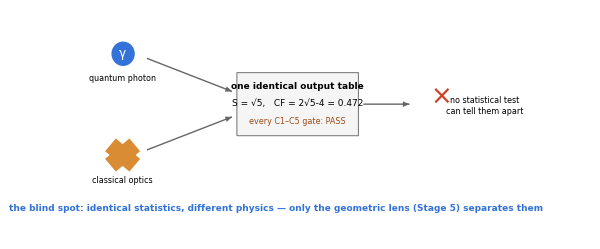

```mathematica
Module[{},
 Graphics[{
   {RGBColor[.2, .45, .85], Disk[{-3.5, 1}, 0.24]}, White, Text[Style["γ", 12], {-3.5, 1}],
   Black, Text[Style["quantum photon", 8], {-3.5, 0.5}],
   {RGBColor[.85, .55, .2], Thickness[0.02], Line[{{-3.75, -0.8}, {-3.25, -1.2}}], Line[{{-3.75, -1.2}, {-3.25, -0.8}}]},
   Black, Text[Style["classical optics", 8], {-3.5, -1.5}],
   Arrowheads[0.028], GrayLevel[0.4],
   Arrow[{{-3.0, 0.9}, {-1.25, 0.25}}], Arrow[{{-3.0, -0.9}, {-1.25, -0.25}}],
   {GrayLevel[0.96], EdgeForm[GrayLevel[0.5]], Rectangle[{-1.15, -0.62}, {1.35, 0.62}]},
   Black, Text[Style["one identical output table", 9, Bold], {0.1, 0.35}],
   Text[Style["S = √5,   CF = 2√5-4 = 0.472", 9], {0.1, 0.02}],
   RGBColor[.6, .3, .1], Text[Style["every C1–C5 gate: PASS", 8], {0.1, -0.34}],
   GrayLevel[0.4], Arrow[{{1.45, 0}, {2.4, 0}}],
   RGBColor[.8, .25, .15], Text[Style["×", 26], {3.05, 0.12}],
   Black, Text[Style["no statistical test", 8], {3.95, 0.08}], Text[Style["can tell them apart", 8], {3.95, -0.15}],
   RGBColor[.2, .45, .85], Text[Style["the blind spot: identical statistics, different physics — only the geometric lens (Stage 5) separates them", 9, Bold], {-0.35, -2.05}]
   }, ImageSize -> 600, PlotRange -> {{-4.4, 5.2}, {-2.4, 1.6}}, ImagePadding -> 6]]
```

Both devices produce exactly the same output table, both node sums equal Sqrt[5], and both contextual fractions equal 2 Sqrt[5] - 4. Every Category-1 gate passes — which means the emulator earns a QUANTUM-CERTIFIED verdict it does not deserve. This is the framework's one designed-in blind spot, and it is the whole reason a second, completely different kind of evidence is needed. Statistics have run out; geometry has not.

## Stage 5 — The Geometric Lens (Proposition 2): How Twisted Is the Motion?

```mathematica
Import[FileNameJoin[{NotebookDirectory[], "figure-gallery", "figures", "leaf_sphere_paper.png"}]]
```

-Graphics-

Figure (Stage 5). The geometric lens, made geometric: one so(3) generator's orbit is the red ring — a one-dimensional leaf, DLA = 1, emulable by a single optical axis — while the full four-generator KCBS cascade fills the 2-sphere, DLA = 3. Static Paper-theme render, recomputed and hard-gated from the verbatim KCBSDirections / CascadeGenerators / So3Axis / DLADimension source (figure-gallery). An interactive version appears below.

The second check does not look at output statistics at all. It looks at the shape of the internal transformations the device claims to perform, using the dynamical Lie algebra [2]: how many independent motions must a classical compiler chain together to reproduce it? A genuine quantum pentagon needs its internal steps to twist in a fully three-dimensional way — the algebra dimension must reach 3. A classical light-splitting fake manages only a flatter, lower-dimensional twist. Re-derive the pentagon's own value directly: first the span the raw steps explore, then the closure after one round of composition.

The pentagon's dynamical Lie algebra: raw span, then commutator closure:

```mathematica
c2 = Cos[Pi/5]/(1 + Cos[Pi/5]);
vecs = Table[{Sqrt[1 - c2] Cos[4 Pi i/5], Sqrt[1 - c2] Sin[4 Pi i/5], Sqrt[c2]}, {i, 0, 4}];
frame = Function[{a, b}, {a, b, Cross[a, b]}];
sf = {frame[vecs[[1]], vecs[[2]]], frame[vecs[[3]], vecs[[2]]], frame[vecs[[3]], vecs[[4]]],
      frame[vecs[[5]], vecs[[4]]], frame[vecs[[5]], vecs[[1]]]};
Ts = Table[sf[[k + 1]] . Transpose[sf[[k]]], {k, 4}];
logs = MatrixLog /@ N[Ts];
axisOf = Function[m, {m[[3, 2]], m[[1, 3]], m[[2, 1]]}];
gens = axisOf /@ logs;
comms = Flatten[Table[axisOf[logs[[i]] . logs[[j]] - logs[[j]] . logs[[i]]], {i, 4}, {j, i + 1, 4}], 1];
{MatrixRank[gens, Tolerance -> 10^-8], MatrixRank[Join[gens, comms], Tolerance -> 10^-8]}
```

{2,3}

{2, 3}: the pentagon's own sequence of measurements explores only a two-dimensional slice of the rotation group, but one extra step of composition closes it into the full three-dimensional group — a fixed number set by the single building block, not by how many copies get composed. This is the '2 to 3 anchor'. The same fact is prettier in space: one generator alone traces a circle (a one-dimensional leaf); the whole cascade fills the sphere.

One motion traces a circle (DLA 1); the full cascade fills the sphere (DLA 3) — drag the step count:

```mathematica
c2 = Cos[Pi/5]/(1 + Cos[Pi/5]);
vecs = Table[{Sqrt[1 - c2] Cos[4 Pi i/5], Sqrt[1 - c2] Sin[4 Pi i/5], Sqrt[c2]}, {i, 0, 4}];
frame = Function[{a, b}, {a, b, Cross[a, b]}];
sf = {frame[vecs[[1]], vecs[[2]]], frame[vecs[[3]], vecs[[2]]], frame[vecs[[3]], vecs[[4]]],
      frame[vecs[[5]], vecs[[4]]], frame[vecs[[5]], vecs[[1]]]};
logs = MatrixLog /@ N[Table[sf[[k + 1]] . Transpose[sf[[k]]], {k, 4}]];
axisOf = Function[m, {m[[3, 2]], m[[1, 3]], m[[2, 1]]}];
gensV = N[axisOf /@ logs];
seedV = N[Normalize[{0.3, 0.6, 0.74}]];
leafV = N[Table[RotationMatrix[t, Normalize[gensV[[1]]]] . seedV, {t, 0, 2 Pi, 2 Pi/160}]];
(* baked in via With, not referenced as outer globals, so the Manipulate is self-contained *)
With[{gens = gensV, seed = seedV, leaf = leafV},
 Manipulate[
  Module[{walk},
   SeedRandom[42];
   walk = NestList[RotationMatrix[0.5, Normalize[gens[[RandomInteger[{1, 4}]]]]] . # &, seed, steps];
   Graphics3D[{
     {Opacity[0.10], RGBColor[.2, .45, .85], Sphere[{0, 0, 0}, 1]},
     {RGBColor[.85, .2, .2], Tube[leaf, 0.012]},
     {GrayLevel[0.3], PointSize[0.011], Point[walk]}
     }, Boxed -> False, PlotRange -> 1.2, ImageSize -> 330,
    PlotLabel -> "red leaf: 1 motion (DLA 1)   •   grey cloud: full cascade (DLA 3)"]],
  {{steps, 300, "cascade steps"}, 20, 1500, 20, Appearance -> "Labeled"},
  ControlPlacement -> Bottom]]
```

A compiler restricted to fewer independent motions than 3 is flagged as intensity-emulable no matter what its click statistics say — which is exactly the audit that catches the tuned cheater of Stage 4. This is gate G7, and it belongs to Category 3 for an honest reason: its input is a declaration about the claimed dynamics, a white-box element, not a black-box observable. It certifies that a claimed mechanism is or is not classically-optically compilable; it does not read the twist off the clicks. Two lenses, not one, is the price of certainty here. A separate result (LP-002) shows the two lenses genuinely answer different questions — their values decorrelate under composition — which is why neither can be dropped.

## Stage 6 — The Construct/Certify Loop: the Optical Constructor

Figure strip (Stage 6). Four blueprints the optical constructor actually emits, each self-certified (VerifyBlueprint returns OK) before export (optical-synthesis):

```mathematica
Import[FileNameJoin[{NotebookDirectory[], "optical-synthesis", "schematics", "demo1_kcbs_pentagon_L1.png"}]]
```

-Graphics-

```mathematica
Import[FileNameJoin[{NotebookDirectory[], "optical-synthesis", "schematics", "demo2_c7_heptagon_L1.png"}]]
```

-Graphics-

```mathematica
Import[FileNameJoin[{NotebookDirectory[], "optical-synthesis", "schematics", "demo3_cct_mesh_reps2.png"}]]
```

-Graphics-

```mathematica
Import[FileNameJoin[{NotebookDirectory[], "optical-synthesis", "schematics", "demo4_table_V0977_L2.png"}]]
```

-Graphics-

Left to right: the Lapkiewicz KCBS pentagon as a Layer-1 Givens / beamsplitter cascade (cos(theta) = 1/GoldenRatio, genuine, so(3) DLA = 3); the C7 heptagon Layer-1 cascade (identity S = 7 - 4 θ(C7)); the cct pentagon-mesh chain at reps = 2 (18 modes, block-local routing); and a pure no-disturbance table at V = 977/1000 realized Layer-2-only (leaf-confined, divided-beam intensity schedule).

To be sure the two checks actually work, the project also built a constructor — the synthesis dual of the test [EMU]. Given a target behaviour it emits an actual optical blueprint: either a genuine particle-based device or a classical light-splitting fake, with exact numbers, so both checks can be run against known, deliberately constructed cases including the Stage-4 cheater tuned to fool you. The KCBS pentagon comes out as the Lapkiewicz interference cascade, and its one design constant is the golden ratio.

The KCBS pentagon in the lab — a single photon across three interferometer paths (Lapkiewicz 2011):

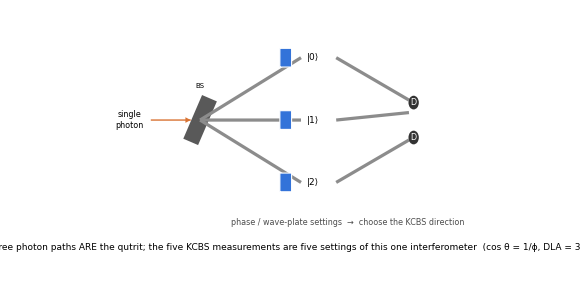

```mathematica
Graphics[{
   {RGBColor[.85, .45, .2], Arrowheads[0.025], Arrow[{{-2.6, 0}, {-1.75, 0}}]},
   Black, Text[Style["single\nphoton", 8], {-3.05, 0}],
   {GrayLevel[0.35], Thickness[0.02], Line[{{-1.75, -0.35}, {-1.35, 0.35}}]}, Text[Style["BS", 7], {-1.55, 0.55}],
   {GrayLevel[0.55], Thickness[0.004], Line[{{-1.55, 0}, {0.6, 1.0}}], Line[{{-1.55, 0}, {0.6, 0}}], Line[{{-1.55, 0}, {0.6, -1.0}}]},
   Black, Text[Style["|0⟩", 9], {0.85, 1.0}], Text[Style["|1⟩", 9], {0.85, 0}], Text[Style["|2⟩", 9], {0.85, -1.0}],
   {RGBColor[.2, .45, .85], EdgeForm[White], Rectangle[{0.15, 0.85}, {0.4, 1.15}], Rectangle[{0.15, -0.15}, {0.4, 0.15}], Rectangle[{0.15, -1.15}, {0.4, -0.85}]},
   GrayLevel[0.3], Text[Style["phase / wave-plate settings  →  choose the KCBS direction", 8], {1.6, -1.65}],
   {GrayLevel[0.55], Thickness[0.004], Line[{{1.35, 1.0}, {2.9, 0.32}}], Line[{{1.35, 0}, {2.9, 0.12}}], Line[{{1.35, -1.0}, {2.9, -0.32}}]},
   {GrayLevel[0.2], Disk[{3.0, 0.28}, 0.11], Disk[{3.0, -0.28}, 0.11]}, White, Text[Style["D", 8], {3.0, 0.28}], Text[Style["D", 8], {3.0, -0.28}],
   Black, Text[Style["three photon paths ARE the qutrit; the five KCBS measurements are five settings of this one interferometer  (cos θ = 1/ϕ, DLA = 3)", 9], {0.3, -2.05}]
   }, ImageSize -> 580, PlotRange -> {{-3.7, 3.9}, {-2.3, 1.5}}, ImagePadding -> 6]
```

So the physical device is a three-path interferometer, not a literal chain of boxes: the '[P, T1, T2, T1, T2]' cascade names the mathematical sequence of SO(3) frame rotations the five sequential measurements trace out — which is what fixes cos θ = 1/GoldenRatio exactly and gives the full so(3) algebra of dimension 3. The intensity-emulator blueprint reproduces the same click table by redistributing brightness and lands with dimension below 3, caught by G7. Every blueprint is re-simulated by an internal verifier that re-audits its own DLA and returns OK only if the reconstruction matches — the A1 through A5 anchors of Category 2. With one building block understood in both directions — tested and constructed — the natural next question is what happens when you chain many of them together.

## Part II — The Composition Theory: the Pentagon-Mesh Algebra

Scaling the atom by gluing. The cis/trans laws, the (cct)^∞ optimal word with gap(cct) = 0.0698975 and its Γ_k certificate ladder, and the physical realization of the winning necklace as a cluster state. Modules: Stages 7-9 and the Interlude. Tracks MESH, CERT, MBQC.

## Stage 7 — Composition: Gluing Pentagons into a Necklace

Interactive (Stage 7) — how you glue decides who wins. Vary the number of glued pentagons and the gluing orientation, and watch the classical-vs-quantum gap survive or vanish. Reused from TheBlackBoxGame.nb:

```mathematica
board2 = Manipulate[
   Module[{nR, tG, cG, idx, tVal, cVal, letter},
     nR = Range[3, 11];
     tG = {0., 0.501381, 0.770178, 0.097889, 0.603730, 1.002762, 0.309729, 0.679151, 1.133615};
     cG = {0., 0., 0.236068, 0., 0.317667, 0., 0.360090, 0., 0.386303};
     idx = nblocks - 2;
     tVal = tG[[idx]]; cVal = cG[[idx]];
     letter = If[orientation == "trans", "Z", "C"];
     Column[{
       Style["gluing word: " <> letter <> "-" <> letter <> "- ... (" <> ToString[nblocks] <> " blocks)", 12],
       ListLinePlot[{Transpose[{nR, tG}], Transpose[{nR, cG}]},
        PlotMarkers -> Automatic, PlotLegends -> {"trans", "cis"},
        Epilog -> {PointSize[0.02], Red, Point[{nblocks, If[orientation == "trans", tVal, cVal]}]},
        AxesLabel -> {"blocks glued", "gap (θ-α)"}, ImageSize -> 380,
        PlotLabel -> "orientation: " <> orientation <> ",  blocks: " <> ToString[nblocks]]
       }]
     ],
   {{nblocks, 5, "blocks glued"}, 3, 11, 1},
   {{orientation, "trans", "gluing orientation"}, {"trans", "cis"}}
   ]
```

If one pentagon shows the gap, what happens if you chain many together, sharing detectors at the joints, like linking pentagon-shaped beads into a necklace? Each joint can be made two ways — 'cis' or 'trans', two ways to attach a bead. The composition itself is pure graph theory: independent copies combine by a co-normal (OR) product, and shared-joint meshes are built by literal graph surgery on the exclusivity graph. The striking finding is that which pattern you use matters far more than how many pentagons you use.

Two pentagon blocks glued at a shared detector — cis and trans are the two ways to attach:

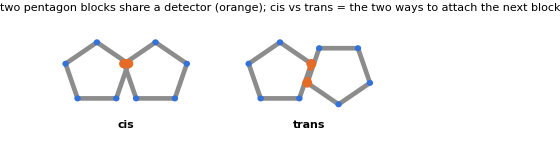

```mathematica
Module[{pentaAt, drawPair},
 pentaAt = Function[{cx, rot}, Table[{cx, 0} + 0.72 {Cos[2 Pi j/5 + rot], Sin[2 Pi j/5 + rot]}, {j, 0, 4}]];
 drawPair = Function[{x0, flip, lbl}, Module[{a, b, ja, jb},
    a = pentaAt[x0, Pi/2];
    b = pentaAt[x0 + 1.28, Pi/2 + flip];
    ja = MaximalBy[a, First][[1]]; jb = MinimalBy[b, First][[1]];
    {{GrayLevel[0.55], Thickness[0.006], Line[Append[a, First[a]]], Line[Append[b, First[b]]]},
     {RGBColor[.2, .45, .85], Disk[#, 0.07] & /@ Join[a, b]},
     {RGBColor[.9, .42, .15], Disk[ja, 0.11], Disk[jb, 0.11], Thickness[0.007], Dashed, Line[{ja, jb}]},
     Black, Text[Style[lbl, 11, Bold], {x0 + 0.64, -1.2}]}]];
 Graphics[{drawPair[0, 0, "cis"], drawPair[4, Pi, "trans"]},
   ImageSize -> 560, PlotRange -> {{-1, 9}, {-1.55, 1.2}}, PlotRangePadding -> 0.1,
   PlotLabel -> "two pentagon blocks share a detector (orange); cis vs trans = the two ways to attach the next block"]]
```

The same gluing at scale — a cct mesh of many blocks (51 blocks = 153 detectors, 204 exclusivities):

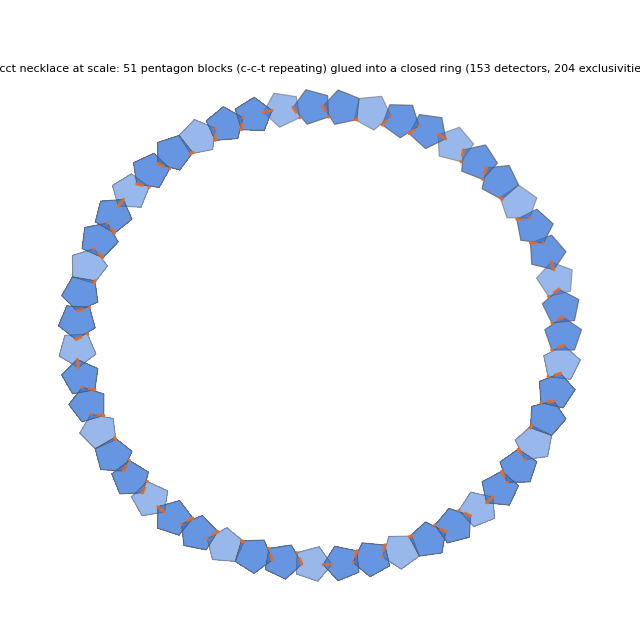

```mathematica
Module[{letters, np, rad, penta, flipSeq, centers, pentagons, joints},
 letters = Characters[StringRepeat["cct", 17]];
 np = Length[letters];
 rad = 0.62 np/(2 Pi);
 penta = Function[{cx, cy, rot}, Table[{cx, cy} + 0.4 {Cos[2 Pi j/5 + rot], Sin[2 Pi j/5 + rot]}, {j, 0, 4}]];
 (* cumulative cis/trans flip, same device as the two-block illustration above: "c" keeps the running
    orientation, "t" flips it by Pi -- so the picture literally traces the real c-c-t word, not a decorative tint *)
 flipSeq = FoldList[If[letters[[#2]] == "t", Mod[#1 + Pi, 2 Pi], #1] &, 0, Range[np]][[1 ;; np]];
 centers = Table[rad {Cos[2 Pi k/np], Sin[2 Pi k/np]}, {k, 0, np - 1}];
 pentagons = Table[penta[centers[[k + 1, 1]], centers[[k + 1, 2]], 2 Pi k/np + Pi/2 + flipSeq[[k + 1]]], {k, 0, np - 1}];
 (* shared-detector joints, same orange dashed convention as the two-block illustration: nearest vertex pair between each glued neighbour *)
 joints = Table[
   Module[{a = pentagons[[k + 1]], b = pentagons[[Mod[k + 1, np] + 1]], ja, jb},
     ja = First[SortBy[a, EuclideanDistance[#, Mean[b]] &]];
     jb = First[SortBy[b, EuclideanDistance[#, Mean[a]] &]];
     {ja, jb}],
   {k, 0, np - 1}];
 Graphics[{
   Table[{RGBColor[.2, .45, .85, If[letters[[k + 1]] == "c", 0.75, 0.5]], EdgeForm[GrayLevel[0.35]],
      Polygon[pentagons[[k + 1]]]}, {k, 0, np - 1}],
   {RGBColor[.9, .42, .15], Opacity[0.85], Thickness[0.0035], Dashed, Line /@ joints},
   {RGBColor[.9, .42, .15], PointSize[0.0035], Point[Flatten[joints, 1]]}
   },
  ImageSize -> 640, PlotRange -> All, AspectRatio -> Automatic,
  PlotLabel -> "a cct necklace at scale: 51 pentagon blocks (c-c-t repeating) glued into a closed ring (153 detectors, 204 exclusivities)"]
]
```

Gluing a ring one way ('trans') keeps a substantial gap open at essentially every size; gluing it the opposite way ('cis') collapses the gap to exactly zero at almost every size — the composed graph becomes as good for a classical hidden-variable model as for a quantum one. Same block count, opposite fate:

Same number of pentagons, opposite outcome — orientation decides the gap:

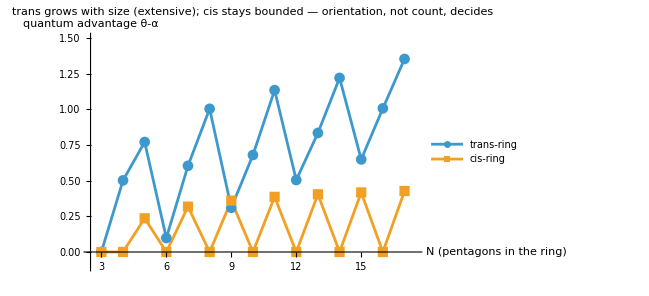

```mathematica
nRange = Range[3, 17];
transGap = {0., 0.5014, 0.7702, 0.0979, 0.6037, 1.0028, 0.3097, 0.6792, 1.1336, 0.5041, 0.8336, 1.2191, 0.6484, 1.0058, 1.3519};
cisGap = {0., 0., 0.2361, 0., 0.3177, 0., 0.3601, 0., 0.3863, 0., 0.4042, 0., 0.4171, 0., 0.4270};
ListLinePlot[{Transpose[{nRange, transGap}], Transpose[{nRange, cisGap}]},
 PlotMarkers -> Automatic, PlotLegends -> {"trans-ring", "cis-ring"},
 AxesLabel -> {"N (pentagons in the ring)", "quantum advantage θ-α"},
 PlotRange -> {{2.5, 17.5}, {-0.1, 1.5}}, ImageSize -> 480, ImagePadding -> {{45, 15}, {40, 28}},
 PlotLabel -> "trans grows with size (extensive); cis stays bounded — orientation, not count, decides"]
```

Read the plot this way: the vertical distance between the two curves at each N is how much quantum advantage the gluing orientation alone costs or keeps. The trans curve grows with N — the advantage is extensive, accumulating as the mesh lengthens — while the cis curve stays bounded and sits at zero for every even N. So orientation, not block count, is the design knob. And neither pure orientation is actually optimal: an explicit alternating gluing pattern — 'cct' repeated forever — was found, by testing tens of thousands of patterns by computer, to preserve the most advantage per pentagon of any pattern tried, beating the best pure orientation by 61%. Measured as the quantum advantage contributed per block:

Quantum advantage per block (gap density): the cct pattern wins:

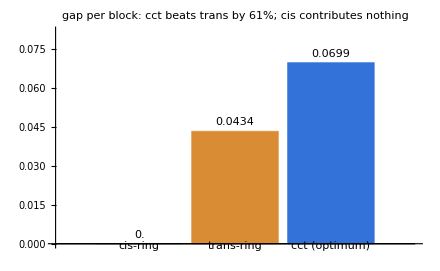

```mathematica
BarChart[{0.0, 0.0433844, 0.0698975},
 ChartLabels -> {"cis-ring", "trans-ring", "cct (optimum)"},
 ChartStyle -> {GrayLevel[.72], RGBColor[.85, .55, .2], RGBColor[.2, .45, .85]},
 PlotRange -> {0, 0.082}, ImageSize -> 440, ImagePadding -> {{48, 20}, {46, 36}},
 LabelingFunction -> (Placed[NumberForm[#, 3], Above] &),
 PlotLabel -> "gap per block: cct beats trans by 61%; cis contributes nothing"]
```

So the wiring pattern is itself a physical design choice with a measurable, sometimes decisive, effect — block-counting alone is not enough. Note also what did not happen here: this whole composition law lives in graph combinatorics, and the geometric Lie-Poisson lens of Stage 5 is applied separately, to the mesh's physical realization. By the project's own result the two do not track each other. That leaves one uncomfortable question: a computer can only test patterns that repeat, so how can 'cct' be called best against the infinitely many patterns that never repeat?

## Stage 8 — Optimization: (cct)^∞ Is Best (Ergodic Optimization)

```mathematica
Import[FileNameJoin[{NotebookDirectory[], "composition-optimality", "orbit_spectrum.png"}]]
```

-Graphics-

Figure (Stage 8). Why cct is special. (A) The periodic-orbit density spectrum from trans tau* = 1.3767 up to cis 3/2, with mixed orbits 16/11, 19/13, 25/17 crowding a narrow band. (B) Seed value against density: spurious strategy-iteration seeds fall on value = density - 1, while the true optimum cct alone drops to density - 4/3 — the gap 0.0698975 (composition-optimality).

A computer search can only check patterns that repeat. But there are infinitely many non-repeating gluing words too, and you cannot brute-force them. The fix is to change what you optimize over. The physical quantity that actually matters — the mesh's advantage per pentagon as it grows without bound — is by definition a long-run average, and the precise name for that is the Birkhoff (ergodic) average of a local potential ϕ that scores the gap contributed by a small window around each junction:

gap(w)  =  lim (1/n) ∑ ϕ(σ^k w),   k = 0 .. n-1

The Birkhoff theorem then converts an intractable search over individual infinite words into a search over shift-invariant probability measures — a compact, convex space that ergodic-optimization theory (Bousch, Mañé, Jenkinson) is built to handle. A periodic word like (cct) repeated forever is just one easy candidate, with a natural measure and a computable average; the honest open question (hypothesis H1) is whether some non-periodic invariant measure could beat every periodic one, a known kind of pathology in this field. The repo's tooling — de Bruijn graphs, max-plus eigenvalues, policy iteration — produces a ladder of certified upper bounds Γ_k that squeeze the optimum from above.

The certificate ladder Γ_k closing on gap(cct) from above:

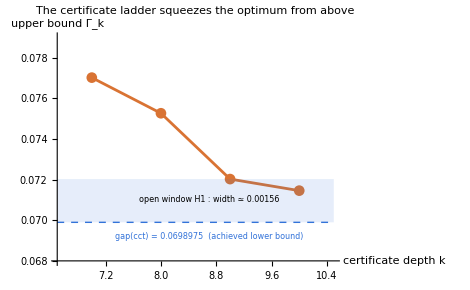

```mathematica
gammaData = {{7, 0.07702057}, {8, 0.07526640}, {9, 0.07202651}, {10, 0.07145754}};
gapcct = 0.0698975;
Show[
 ListLinePlot[gammaData, PlotMarkers -> Automatic, PlotStyle -> RGBColor[.85, .45, .2],
  PlotRange -> {{6.5, 10.5}, {0.068, 0.079}},
  AxesLabel -> {"certificate depth k", "upper bound Γ_k"}, ImageSize -> 470],
 Graphics[{
   {RGBColor[.2, .45, .85, 0.12], Rectangle[{6.5, gapcct}, {10.5, 0.07202651}]},
   {RGBColor[.2, .45, .85], Dashed, Line[{{6.5, gapcct}, {10.5, gapcct}}]},
   Text[Style["gap(cct) = 0.0698975  (achieved lower bound)", 8, RGBColor[.2, .45, .85]], {8.7, 0.0692}],
   Text[Style["open window H1 : width ≃ 0.00156", 8], {8.7, 0.0710}]}],
 PlotLabel -> "The certificate ladder squeezes the optimum from above"]
```

By depth ten the certified gap between the best provable upper bound and the value cct actually achieves is down to 0.00156. It is not fully closed — H1 remains an open hypothesis — but it is boxed in extremely tightly. The mechanism the certificate rests on is just the sliding window: run it along the infinite word and average the local gap, and the running mean settles onto the per-block value.

The Birkhoff average made concrete — slide a window along (cct) repeated and watch the running gap settle:

```mathematica
Manipulate[
 Module[{seq, phi, run, lim = 0.0698975},
  seq = Flatten[ConstantArray[{"c", "c", "t"}, 40]];
  phi = seq /. {"c" -> 0.093, "t" -> 0.023695};
  run = Accumulate[Take[phi, n]]/Range[n];
  Column[{
    Row[Take[seq, Min[n, 15]] /. {"c" -> Style["c", RGBColor[.2, .45, .85], Bold],
        "t" -> Style["t", RGBColor[.85, .55, .2], Bold]}, Spacer[2]],
    Show[
     ListLinePlot[run, PlotStyle -> Directive[RGBColor[.2, .45, .85], Thickness[0.006]], Joined -> True,
      PlotRange -> {{0, 120}, {0, 0.11}}, AxesLabel -> {"n", "advantage / block"},
      ImageSize -> 480, ImagePadding -> {{55, 25}, {42, 26}},
      PlotLabel -> Row[{"running average after ", n, " blocks = ", NumberForm[Last[run], {4, 4}], "   (moving → fixed target)"}]],
     Graphics[{{RGBColor[.85, .55, .2], Dashed, Line[{{0, lim}, {120, lim}}]},
       {RGBColor[.85, .55, .2], Text[Style["fixed target: gap(cct) = 0.0699  (the n → ∞ limit)", 9], {58, lim + 0.012}]},
       {RGBColor[.2, .45, .85], PointSize[0.02], Point[{Min[n, 120], Last[run]}]}}]]
    }]],
 {{n, 14, "blocks averaged n  (1 to 120)"}, 1, 120, 1, Appearance -> "Labeled"},
 ControlPlacement -> Bottom]
```

Why the limit, and not a finite mesh? A mesh of any finite size gives only a partial average, and its value drifts depending on where you stop reading the word. Only the n → ∞ limit is a property of the pattern itself rather than of an arbitrary cutoff — and a larger limit means more quantum advantage kept per pentagon, forever, as the mesh grows without bound. That single number is exactly what Stage 8 optimizes across all gluing patterns, which is why cct's limit of 0.0699 is the value to beat. (The per-junction values here are a toy potential chosen only so the period average lands on gap(cct); the point is the convergence, not the decomposition.) With cct established as the best repeating blueprint, the next move is to build it as something physical.

## Interlude — A Bookkeeping View: Gluing Words as a Multiway System

A note on method, since the question naturally comes up: where do ruliology and multiway systems fit here? Exactly one layer of the story is genuinely a symbolic dynamical system, and it is this one. The gluing words over the alphabet {c, t}, the shift that shows the mesh growing one block at a time, and the de Bruijn graphs behind the Γ_k certificates of Stage 8 form a multiway/substitution system in the literal sense — not by analogy. Treating it that way is honest bookkeeping; it is not a claim that the pentagon's continuous machinery is a rewrite rule, as the end of this interlude is careful to say.

The gluing alphabet as a de Bruijn multiway graph; the cct optimum is a periodic orbit:

```mathematica
alph = {"c", "t"};
words = StringJoin /@ Tuples[alph, 3];
shift = Function[{w, a}, StringTake[w, -2] <> a];
dbEdges = DeleteDuplicates[Flatten[Table[DirectedEdge[w, shift[w, a]], {w, words}, {a, alph}]]];
orbit = {"cct", "ctc", "tcc"};
orbitEdges = DirectedEdge @@@ Partition[Append[orbit, First[orbit]], 2, 1];
Graph[words, dbEdges, VertexLabels -> "Name", VertexSize -> 0.45,
 VertexStyle -> GrayLevel[0.85], EdgeStyle -> GrayLevel[0.8],
 GraphHighlight -> Join[orbit, orbitEdges], GraphHighlightStyle -> "Thick",
 GraphLayout -> "CircularEmbedding", ImageSize -> 480,
 ImagePadding -> {{55, 25}, {25, 55}}, PlotRangePadding -> Scaled[0.08],
 PlotLabel -> Style["de Bruijn-3 graph over {c,t}: sliding (cct) traces the highlighted cycle", 12]]
```

-Graphics-

Each edge is one step of the shift: drop the oldest letter, read the next. The word (cct) repeated forever is the highlighted three-cycle, and Stage 8's ergodic optimization is precisely optimization over shift-invariant measures on this graph. A periodic word is a measure supported on one cycle; the open part of H1 is whether some non-periodic invariant measure — an orbit that never settles into any finite cycle — could beat every periodic one. The multiway picture is what makes that question well-posed rather than hand-wavy.

The same picture gives a clean way to ask whether the essay's two lenses are, underneath, the same system. Put both readings on one rewrite: let each state carry its exclusivity graph and its dynamical Lie algebra, and let the single move be 'glue one more block'. The correlation lens is one projection of that system (the contextual-fraction density); the geometric lens is another (the DLA). If the two moved together, the projection of the rewrite would be a morphism — a commuting square.

Two projections of one gluing rule; a morphism would make the square commute:

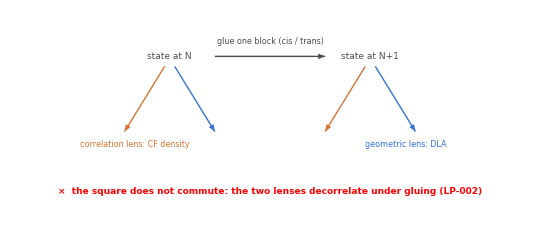

```mathematica
Graphics[{
   Arrowheads[0.028], GrayLevel[0.3],
   Text[Style["state at N", 9], {0, 2}], Text[Style["state at N+1", 9], {4, 2}],
   Arrow[{{0.9, 2}, {3.1, 2}}], Text[Style["glue one block (cis / trans)", 8], {2, 2.3}],
   RGBColor[.85, .45, .2], Arrow[{{-0.1, 1.8}, {-0.9, 0.5}}], Arrow[{{3.9, 1.8}, {3.1, 0.5}}],
   Text[Style["correlation lens: CF density", 8], {-0.7, 0.25}],
   RGBColor[.2, .45, .85], Arrow[{{0.1, 1.8}, {0.9, 0.5}}], Arrow[{{4.1, 1.8}, {4.9, 0.5}}],
   Text[Style["geometric lens: DLA", 8], {4.7, 0.25}],
   Red, Text[Style["×  the square does not commute: the two lenses decorrelate under gluing (LP-002)", 9, Bold], {2, -0.7}]
   }, ImageSize -> 540, PlotRange -> {{-2.4, 6.4}, {-1.1, 2.7}}]
```

The same nine composed meshes, projected both ways — the correlation even flips sign:

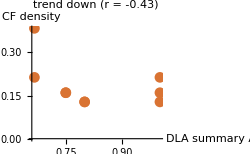
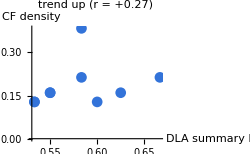

```mathematica
satFrac = {1.0000, 1.0000, 1.0000, 0.6667, 0.7500, 0.8000, 0.6667, 0.7500, 0.8000};
auc = {0.6667, 0.6250, 0.6000, 0.5833, 0.5500, 0.5333, 0.5833, 0.5500, 0.5333};
cfDensity = {0.2130, 0.1597, 0.1278, 0.2130, 0.1597, 0.1278, 0.3832, 0.1597, 0.1278};
panelA = ListPlot[Transpose[{satFrac, cfDensity}], PlotStyle -> RGBColor[.85, .45, .2],
   PlotMarkers -> Automatic, AxesLabel -> {"DLA summary A", "CF density"},
   PlotLabel -> "trend down  (r = -0.43)", ImageSize -> 250];
panelB = ListPlot[Transpose[{auc, cfDensity}], PlotStyle -> RGBColor[.2, .45, .85],
   PlotMarkers -> Automatic, AxesLabel -> {"DLA summary B", "CF density"},
   PlotLabel -> "trend up  (r = +0.27)", ImageSize -> 250];
Row[{panelA, panelB}, Spacer[12]]
```

The same nine meshes, the same correlation coordinate; only the choice of how to summarize the geometric-lens evolution differs, and the trend reverses. There is no monotone map from one lens's evolution to the other's, so the square does not commute — which is the point. The ruliological deliverable here is not a commuting diagram but the vivid failure of one, and it dramatizes a headline result rather than decorating it. That is also the boundary of the method: multiway and cellular-automaton pictures are faithful for the symbolic layer — the words, the shift, the certificate graphs, the clique search — and illustrative only for the continuous layer, where cos θ = 1/ϕ, √5, and the DLA closure come from linear algebra and graph invariants, not from any rewrite rule. Bookkeeping, kept in its place.

## Stage 9 — Realization: From Best Necklace to a Cluster-State Resource

Since 'cct forever' is the best blueprint, the next step is to build it as a real entangled quantum resource: a cluster state, the kind of resource used in measurement-based quantum computing, and then verify its structure holds up even at millions of components. The connectivity is the glued-mesh graph itself, now read as a pattern of controlled-Z entangling bonds.

The cct cluster state as a CZ-entangled pentagon chain:

```mathematica
wordRing = Function[{word, reps}, Module[{w = Characters[StringRepeat[word, reps]], L, edges = {}, u, v, km},
   L = Length[w];
   Do[km = Mod[k - 1, L];
     {u, v} = If[w[[km + 1]] === "c", {3 km + 1, 3 km + 2}, {3 km + 2, 3 km + 1}];
     edges = Join[edges, {{u, v}, {u, 3 k + 1}, {3 k + 1, 3 k + 2}, {3 k + 2, 3 k + 3}, {3 k + 3, v}}],
     {k, 0, L - 1}];
   Graph[Range[3 L], UndirectedEdge @@@ DeleteDuplicates[Sort /@ edges]]]];
Graph[wordRing["cct", 4], VertexSize -> 0.6, VertexStyle -> RGBColor[.2, .45, .85],
 EdgeStyle -> GrayLevel[0.6], GraphLayout -> "SpringElectricalEmbedding", ImageSize -> 430,
 PlotLabel -> "cct cluster connectivity (CZ bonds), (cct) repeated four times"]
```

-Graphics-

Verifying such a resource has two regimes, and it is worth being honest about both. The dense many-body approach is exact but explodes: a single pentagon's multi-qubit algebra already fills dimension 1023 = 4⁵ - 1, and eight blocks would need on the order of a hundred gigabytes. The sparse stabilizer path sidesteps that and scales:

Two regimes for verifying the cluster — the exact one caps out, the sparse one scales:

```mathematica
Module[{green = RGBColor[0.24, 0.55, 0.36], amber = RGBColor[0.80, 0.50, 0.18],
   navy = RGBColor[0.16, 0.28, 0.46], ink = GrayLevel[0.18], dot, g},
 dot[c_] := Style["● ", c, 13];
 g = Grid[{
    {Style["regime", White, Bold, 11, FontFamily -> "Helvetica"],
     Style["reach", White, Bold, 11, FontFamily -> "Helvetica"]},
    {Row[{dot[amber], "dense many-body DLA (exact)"}],
     "1 pentagon → dim 1023 = 4⁵-1;  8 blocks ≃ 137 GiB → infeasible"},
    {Row[{dot[green], "sparse stabilizer path"}],
     "structure verified to 27,000,000 qubits / 9,000,000 pentagons in ≃ 312 s"}
    },
   Background -> {None, {navy, White, GrayLevel[0.965]}},
   Frame -> None,
   Dividers -> {None, {2 -> Directive[GrayLevel[0.8], Thin]}},
   Alignment -> Left,
   ItemStyle -> Directive[FontFamily -> "Helvetica", 11, ink],
   Spacings -> {2.2, 1.8}, ItemSize -> {{22, 55}, Automatic}];
 Framed[g, FrameStyle -> None, FrameMargins -> {{0, 0}, {8, 0}}, Background -> White]
]
```

regime | reach
● dense many-body DLA (exact) | 1 pentagon → dim 1023 = 4⁵-1;  8 blocks ≃ 137 GiB → infeasible
● sparse stabilizer path | structure verified to 27,000,000 qubits / 9,000,000 pentagons in ≃ 312 s

The blueprint is not just optimal on paper; its entanglement structure holds up under verification into the millions of components (gate G6, the MBQC back-end). That settles the main line of the story. Two side questions remain — whether the pentagon is special among shapes, and whether it can do something to structures much larger than itself.

## Part III — The Activation Frontier

Where Global Exclusivity at k copies meets the Lovász number θ(G): products, dormancy, and pentagon catalysis to ω = 17. Numerics-only by design. Modules: Stages 10-11. Track D1.

## Stage 10 — Frontier: Products and Dormancy

In parallel, a separate line asked whether the pentagon's behaviour is special or whether bigger shapes — seven-sided, nine-sided — behave the same when you combine several independent copies. This uses the co-normal product rather than shared-joint gluing: take several independent copies and connect events whenever any single coordinate is adjacent. Two copies of the pentagon already suffice to reach the quantum value: one copy tops out at 5/2, but the two-copy product carries a clique of size five that pulls the global exclusivity bound down to √5.

A gallery of GE exclusivity 'molecules' — co-normal products of cycles, drawn as nested rings:

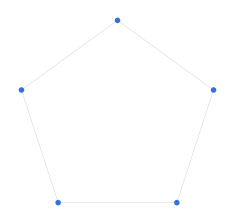
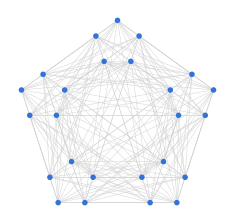
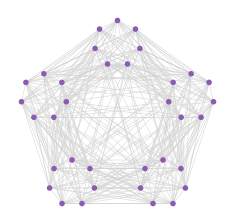
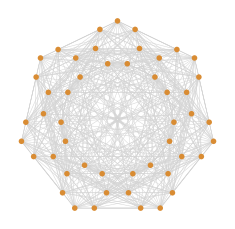
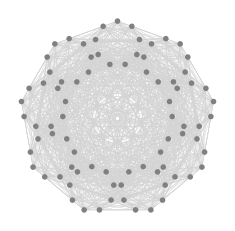
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics3D-

```mathematica
Module[{mol, pos3D, verts775, coords775, witIdx775, witCoords775},
 mol = Function[{ns, radii, col, lbl}, Module[{verts, coords, adj, epairs, nv},
    verts = Tuples[Range[0, # - 1] & /@ ns];
    nv = Length[verts];
    coords = Table[Sum[radii[[i]] {Cos[2 Pi verts[[v, i]]/ns[[i]] + Pi/2], Sin[2 Pi verts[[v, i]]/ns[[i]] + Pi/2]}, {i, Length[ns]}], {v, nv}];
    adj = Function[{u, w}, Or @@ MapThread[MemberQ[{1, #3 - 1}, Mod[#1 - #2, #3]] &, {u, w, ns}]];
    epairs = Select[Subsets[Range[nv], {2}], adj[verts[[#[[1]]]], verts[[#[[2]]]]] &];
    Labeled[Graphics[{
       {GrayLevel[0.83], AbsoluteThickness[0.35], Line[coords[[#]]] & /@ epairs},
       {col, AbsolutePointSize[4], Point[coords]}}, ImageSize -> 235, PlotRange -> All, PlotRangePadding -> Scaled[0.04]],
     Column[{Style[lbl, Bold, 9], Style[ToString[nv] <> " events • " <> ToString[Length[epairs]] <> " edges", 8, GrayLevel[0.45]]}, Alignment -> Center], Bottom]]];
 pos3D[idx_, ns_, r_] := Module[{th},
   th = MapThread[2 Pi #1/#2 &, {idx, ns}];
   r[[1]] {Cos[th[[1]]], Sin[th[[1]]], 0} + r[[2]] {0, Cos[th[[2]]], Sin[th[[2]]]} + r[[3]] {Cos[th[[3]]], 0, Sin[th[[3]]]}];
 verts775 = Tuples[Range[0, # - 1] & /@ {7, 7, 5}];
 coords775 = pos3D[#, {7, 7, 5}, {2.2, 1.4, 0.7}] & /@ verts775;
 witIdx775 = Position[verts775, #][[1, 1]] & /@ {{0,1,1},{1,3,3},{2,0,1},{3,2,3},{4,4,0},{5,0,2},{5,1,2},{6,5,2},{6,6,4}};
 witCoords775 = coords775[[witIdx775]];
 Grid[{
   {mol[{5}, {1}, RGBColor[.2, .45, .85], "C5  (the atom)"],
    mol[{5, 5}, {3.1, 0.9}, RGBColor[.2, .45, .85], "C5 ⊗ C5"],
    mol[{5, 7}, {3.2, 0.95}, RGBColor[.55, .35, .7], "C5 ⊗ C7"]},
   {mol[{7, 7}, {3.2, 0.95}, RGBColor[.85, .55, .2], "C7 ⊗ C7"],
    mol[{9, 9}, {3.2, 0.95}, RGBColor[.5, .5, .5], "C9 ⊗ C9  (dormant)"],
    Labeled[Graphics3D[{
       {GrayLevel[0.6], Opacity[0.5], PointSize[0.011], Point[coords775]},
       {RGBColor[.75, .25, .25], Opacity[0.55], Thickness[0.0045], Line[{witCoords775[[#[[1]]]], witCoords775[[#[[2]]]]}] & /@ Subsets[Range[9], {2}]},
       {RGBColor[.75, .25, .25], PointSize[0.022], Point[witCoords775]}
       }, Boxed -> False, ImageSize -> 235, SphericalRegion -> True, ViewPoint -> {1.5, -2.2, 1.4}],
     Column[{Style["C7 ⊗ C7 ⊗ C5", Bold, 9], Style["9-clique witness, real 3-torus (drag to rotate)", 8, GrayLevel[0.45]]}, Alignment -> Center], Bottom]}},
  Spacings -> {1.4, 1.4}]]
```

This 'ACTIVATES' verdict is not only a graph fact. The project's own black-box certifier wires exactly this construction — the two-copy exclusivity graph above, 535 maximal cliques, ten of them pentads — into a real pass/fail test: sum the joint probability over each pentad, and flag the device the moment any sum passes 1.

Run live, on two tables: the quantum-optimal one, and the one a classical light-splitter reports when it mistakes intensity fractions for click probabilities (Wright's table):

```mathematica
verts = Tuples[Range[1, 5], 2];
adj = Function[{u, w}, Or @@ MapThread[MemberQ[{1, 4}, Mod[#1 - #2, 5]] &, {u, w}]];
epairs = Select[Subsets[verts, {2}], adj[#[[1]], #[[2]]] &];
cliques = FindClique[Graph[verts, UndirectedEdge @@@ epairs], Infinity, All];
pentads = Select[cliques, Length[#] == 5 &];
loadOf[p_] := Max[Table[Total[(p[[#[[1]]]] p[[#[[2]]]]) & /@ K], {K, pentads}]];
{qLoad, wLoad} = {loadOf[ConstantArray[1/Sqrt[5], 5]], loadOf[ConstantArray[1/2, 5]]};
Module[{green = RGBColor[0.24, 0.55, 0.36], red = RGBColor[0.75, 0.30, 0.24],
   navy = RGBColor[0.16, 0.28, 0.46], ink = GrayLevel[0.18], badge, g},
 badge[label_, c_] := Framed[Style[label, 10, White, FontFamily -> "Helvetica", Bold],
    Background -> c, RoundingRadius -> 10, FrameStyle -> None, FrameMargins -> {{9, 9}, {3, 3}}];
 g = Grid[{
    {Style["table", White, Bold, 11, FontFamily -> "Helvetica"],
     Style["per-event p", White, Bold, 11, FontFamily -> "Helvetica"],
     Style["worst pentad load", White, Bold, 11, FontFamily -> "Helvetica"],
     Style["verdict", White, Bold, 11, FontFamily -> "Helvetica"]},
    {"quantum-optimal", 1/Sqrt[5], qLoad, badge["safe (saturates)", green]},
    {"intensity fractions (Wright)", 1/2, wLoad, badge["EMULATION-SUSPECT", red]}
    },
   Background -> {None, {navy, White, GrayLevel[0.965]}},
   Frame -> None,
   Dividers -> {None, {2 -> Directive[GrayLevel[0.8], Thin]}},
   Alignment -> {{Left, Center, Center, Center}, Center},
   ItemStyle -> Directive[FontFamily -> "Helvetica", 11, ink],
   Spacings -> {2.2, 2}, ItemSize -> {Automatic, 2.2}];
 Framed[g, FrameStyle -> None, FrameMargins -> {{0, 0}, {8, 0}}, Background -> White]
]
```

table | per-event p | worst pentad load | verdict
quantum-optimal | 1/(√5) | 1 | safe (saturates)
intensity fractions (Wright) | 1/2 | 5/4 | EMULATION-SUSPECT

The same two numbers, against the bound:

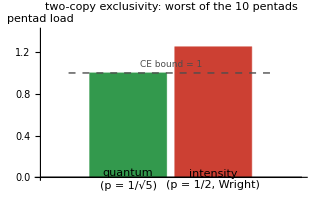

```mathematica
Show[
  BarChart[{qLoad, wLoad}, ChartLabels -> {"quantum
(p = 1/√5)", "intensity
(p = 1/2, Wright)"},
   ChartStyle -> {RGBColor[.2, .6, .3], RGBColor[.8, .25, .2]},
   PlotRange -> {0, 1.4}, ImageSize -> 320, ImagePadding -> {{45, 15}, {45, 20}},
   AxesLabel -> {None, "pentad load"},
   PlotLabel -> "two-copy exclusivity: worst of the 10 pentads"],
  Graphics[{GrayLevel[0.3], Dashed, Line[{{0.3, 1}, {2.7, 1}}],
    Text[Style["CE bound = 1", 9, GrayLevel[0.3]], {1.5, 1.08}]}]
  ]
```

25% over budget is a mathematical proof, not a judgement call: no genuine quantum pair of pentagons can produce that number, so a device reporting it is certifiably not what it claims to be. But the catch is the same one Stage 4 already found for a single copy: an intensity emulator tuned to the exact quantum fraction, p = 1/√5, reproduces this test number-for-number — its worst pentad also saturates at 1, not past it — and the verdict comes back QUANTUM-CERTIFIED. Catching that particular fake needs the geometric lens, not another probability sum; that is the entire reason the instrument carries two lenses rather than one.

There is a known general theorem, though: for large enough cycles — nine-sided or larger — combining independent copies this way never creates a bigger advantage, and the effect stays dormant. The research maps where composition does and does not wake it, across several concrete structures — pentagon and heptagon products, the four-pentagon Quad-C5 graph, the nonagon join that Stage 11 switches on, and a Paley-graph case that is still open:

The composition variants studied — which structures wake the effect, and which stay dormant:

```mathematica
Module[{green = RGBColor[0.24, 0.55, 0.36], amber = RGBColor[0.80, 0.50, 0.18],
   gray = GrayLevel[0.55], navy = RGBColor[0.16, 0.28, 0.46], ink = GrayLevel[0.18], badge, rowBg},
 badge[label_, c_] := Framed[Style[label, 10, White, FontFamily -> "Helvetica", Bold],
    Background -> c, RoundingRadius -> 10, FrameStyle -> None,
    FrameMargins -> {{9, 9}, {3, 3}}];
 rowBg = Join[{navy}, Table[If[OddQ[i], White, GrayLevel[0.965]], {i, 1, 6}]];
 Grid[{
   {Style["structure", White, Bold, 11, FontFamily -> "Helvetica"],
    Style["construction", White, Bold, 11, FontFamily -> "Helvetica"],
    Style["result", White, Bold, 11, FontFamily -> "Helvetica"],
    Style["verdict", White, Bold, 11, FontFamily -> "Helvetica"]},
   {"C5⊗C5", "two pentagon copies (co-normal)",
    Row[{"ω = 5 → reaches ", Sqrt[5]}], badge["ACTIVATES", green]},
   {"C7⊗C7⊗C5", "two heptagon copies + one pentagon (co-normal)",
    Row[{"9-clique, load 9", Sqrt[5], "/20 ≃ 1.006 > 1"}], badge["ACTIVATES (mix)", green]},
   {"Quad-C5", "four-pentagon graph (arXiv:2605.12828)",
    "θ = 3.468,  Δ = 0.468", badge["ACTIVATES", green]},
   {"C9⋁C9⋁C9⋁C5", "three nonagons + one pentagon (co-normal)",
    "clique ≥ 17 = 2⁴+1  (Stage 11)", badge["ACTIVATES (catalysis)", green]},
   {"Paley(13)⋁3", "Paley-13, co-normal cube (3 copies)",
    "ω bracketed in [39, 46]", badge["OPEN", amber]},
   {"C9⊗C9", "nonagon copies alone",
    "never exceed the bound", badge["DORMANT", gray]}
   },
  Background -> {None, rowBg},
  Frame -> None,
  Dividers -> {None, {2 -> Directive[GrayLevel[0.8], Thin]}},
  Alignment -> {{Left, Left, Left, Center}, Center},
  ItemStyle -> Directive[FontFamily -> "Helvetica", 11, ink],
  Spacings -> {2, 1.6},
  ItemSize -> {Automatic, 1.7},
  ImageSize -> 680
  ]
]
```

structure | construction | result | verdict
C5⊗C5 | two pentagon copies (co-normal) | ω = 5 → reaches √5 | ACTIVATES
C7⊗C7⊗C5 | two heptagon copies + one pentagon (co-normal) | 9-clique, load 9√5/20 ≃ 1.006 > 1 | ACTIVATES (mix)
Quad-C5 | four-pentagon graph (arXiv:2605.12828) | θ = 3.468,  Δ = 0.468 | ACTIVATES
C9⋁C9⋁C9⋁C5 | three nonagons + one pentagon (co-normal) | clique ≥ 17 = 2⁴+1  (Stage 11) | ACTIVATES (catalysis)
Paley(13)⋁3 | Paley-13, co-normal cube (3 copies) | ω bracketed in [39, 46] | OPEN
C9⊗C9 | nonagon copies alone | never exceed the bound | DORMANT

Quad-C5 is a specific literature graph, drawn as its four constituent pentagons in 3D. Paley(13)'s three-fold co-normal power is genuinely 3D too, with an explicit 39-clique (evidenced optimal, though [39,46] is not fully closed):

```mathematica
Module[{quadC5, paleyC5},
 quadC5 = Module[{hub2, hub6, hub3, hub7, mid23, perp23, leaf0, leaf5, mid67, perp67, leaf1, leaf4, coordAssoc, pentagons, colors, center, bentEdgePts},
   hub2 = {1, 1, 1}; hub6 = {1, -1, -1}; hub3 = {-1, -1, 1}; hub7 = {-1, 1, -1};
   mid23 = (hub2 + hub3)/2; perp23 = Normalize[Cross[hub3 - hub2, {0, 0, 1}]];
   leaf0 = mid23 + 0.55 perp23 + 0.25 Normalize[hub2 - hub3];
   leaf5 = mid23 - 0.55 perp23 - 0.25 Normalize[hub2 - hub3];
   mid67 = (hub6 + hub7)/2; perp67 = Normalize[Cross[hub7 - hub6, {0, 0, 1}]];
   leaf1 = mid67 + 0.55 perp67 + 0.25 Normalize[hub6 - hub7];
   leaf4 = mid67 - 0.55 perp67 - 0.25 Normalize[hub6 - hub7];
   coordAssoc = <|0 -> leaf0, 1 -> leaf1, 2 -> hub2, 3 -> hub3, 4 -> leaf4, 5 -> leaf5, 6 -> hub6, 7 -> hub7|>;
   pentagons = {{0, 3, 6, 2, 5}, {0, 3, 7, 2, 5}, {1, 4, 7, 2, 6}, {1, 4, 7, 3, 6}};
   colors = {RGBColor[.2, .45, .85], RGBColor[.85, .55, .2], RGBColor[.4, .6, .3], RGBColor[.75, .25, .25]};
   center = Mean[Values[coordAssoc]];
   bentEdgePts[a_, b_, k_] := Module[{pa, pb, mid, dir, outward, perp, offsetMag},
     pa = coordAssoc[a]; pb = coordAssoc[b]; mid = (pa + pb)/2;
     dir = Normalize[pb - pa]; outward = Normalize[mid - center];
     perp = Normalize[outward - (outward . dir) dir]; offsetMag = 0.16 (k - 2.5);
     {pa, mid + offsetMag perp, pb}];
   Labeled[Graphics3D[{
      Table[{colors[[k]], Thickness[0.009], Opacity[0.9],
        Table[BSplineCurve[bentEdgePts[pentagons[[k, m]], pentagons[[k, Mod[m, 5] + 1]], k], SplineDegree -> 2], {m, 5}]}, {k, 4}],
      {GrayLevel[0.2], Sphere[coordAssoc[#], 0.14] & /@ Range[0, 7]},
      Table[Text[Style[i, 10, White, Bold], coordAssoc[i]], {i, 0, 7}]
      }, Boxed -> False, ImageSize -> 235, SphericalRegion -> True, ViewPoint -> {1.6, -2.4, 1.2}],
    Column[{Style["Quad-C5", Bold, 9], Style["4 pentagons, each edge shared by 2 (arXiv:2605.12828)", 8, GrayLevel[0.45]]}, Alignment -> Center], Bottom]];
 paleyC5 = Module[{qr, adj13, pos3D13, verts13, coords13, clique13, clique39, witIdx, witCoords},
   qr = DeleteDuplicates[Mod[Range[1, 12]^2, 13]];
   adj13 = Table[If[i == j, 0, If[MemberQ[qr, Mod[i - j, 13]], 1, 0]], {i, 0, 12}, {j, 0, 12}];
   pos3D13[idx_, r_] := Module[{th}, th = 2 Pi idx/13;
     r[[1]] {Cos[th[[1]]], Sin[th[[1]]], 0} + r[[2]] {0, Cos[th[[2]]], Sin[th[[2]]]} + r[[3]] {Cos[th[[3]]], 0, Sin[th[[3]]]}];
   verts13 = Tuples[Range[0, 12], 3];
   coords13 = pos3D13[#, {2.3, 1.5, 0.8}] & /@ verts13;
   clique13 = {{0, 4}, {1, 6}, {2, 8}, {3, 10}, {4, 12}, {5, 1}, {6, 3}, {7, 5}, {8, 7}, {9, 9}, {10, 11}, {11, 0}, {12, 2}};
   clique39 = Flatten[Table[Append[ab, c], {ab, clique13}, {c, {0, 1, 4}}], 1];
   witIdx = Position[verts13, #][[1, 1]] & /@ clique39;
   witCoords = coords13[[witIdx]];
   Labeled[Graphics3D[{
      {GrayLevel[0.7], Opacity[0.25], PointSize[0.005], Point[coords13]},
      {RGBColor[.55, .35, .7], Opacity[0.12], Thickness[0.0012], Line[{witCoords[[#[[1]]]], witCoords[[#[[2]]]]}] & /@ Subsets[Range[39], {2}]},
      {RGBColor[.55, .35, .7], PointSize[0.013], Point[witCoords]}
      }, Boxed -> False, ImageSize -> 235, SphericalRegion -> True, ViewPoint -> {1.5, -2.2, 1.4}],
    Column[{Style["Paley(13) co-normal cube", Bold, 9], Style["explicit 39-clique, evidenced tight • OPEN [39,46]", 8, GrayLevel[0.45]]}, Alignment -> Center], Bottom]];
 Grid[{{quadC5, paleyC5}}, Spacings -> {1.4, 1.4}]]
```

-Graphics3D- | -Graphics3D-

C9⋁C9⋁C9⋁C5 is 4-dimensional — three C9 factors plus the pentagon catalyst. Rather than dragging a slider through the fourth dimension by hand, this native animation plays a genuine 4D double rotation automatically — simultaneous rotation in two orthogonal planes, the one motion that only exists in four dimensions or more:

```mathematica
Animate[
 Module[{pos4D, rot4D, project, bgIdx, bg4D, witness17, wit4D, edgesAll, bgP, witP},
  pos4D[idx_] := Module[{th}, th = 2 Pi idx/{9, 9, 9, 5};
    {1.0 Cos[th[[1]]], 1.0 Sin[th[[1]]], 0, 0} + {0, 0, 0.8 Cos[th[[2]]], 0.8 Sin[th[[2]]]} +
    {0.65 Cos[th[[3]]], 0, 0.65 Sin[th[[3]]], 0} + {0, 0.4 Cos[th[[4]]], 0, 0.4 Sin[th[[4]]]}];
  rot4D[{x_, y_, z_, w_}, alpha_, beta_] := {x Cos[alpha] - w Sin[alpha], y Cos[beta] - z Sin[beta],
    y Sin[beta] + z Cos[beta], x Sin[alpha] + w Cos[alpha]};
  project[{x_, y_, z_, w_}, d_: 4.0] := {x, y, z} d/(d - w);
  bgIdx = Tuples[{Range[0, 8, 3], Range[0, 8, 3], Range[0, 8, 3], Range[0, 4]}];
  bg4D = pos4D /@ bgIdx;
  witness17 = {{0, 0, 0, 0}, {2, 4, 4, 1}, {4, 3, 4, 1}, {6, 7, 3, 1}, {6, 7, 8, 2}, {7, 6, 8, 2}, {7, 8, 7, 2}, {8, 6, 6, 2},
     {8, 7, 7, 2}, {1, 2, 2, 3}, {3, 1, 2, 3}, {3, 6, 1, 3}, {4, 8, 3, 3}, {5, 5, 1, 3}, {5, 5, 6, 4}, {7, 7, 5, 4}, {8, 8, 5, 4}};
  wit4D = pos4D /@ witness17;
  edgesAll = Subsets[Range[17], {2}];
  bgP = project[rot4D[#, tt, tt]] & /@ bg4D;
  witP = project[rot4D[#, tt, tt]] & /@ wit4D;
  Graphics3D[{
    {GrayLevel[0.6], Opacity[0.35], PointSize[0.008], Point[bgP]},
    {RGBColor[.2, .45, .85], Opacity[0.6], Thickness[0.005], Line[{witP[[#[[1]]]], witP[[#[[2]]]]}] & /@ edgesAll},
    {RGBColor[.85, .3, .15], PointSize[0.026], Point[witP]}
    }, Boxed -> False, ImageSize -> 650, SphericalRegion -> True, PlotRange -> 3.2, PerformanceGoal -> "Speed",
   PlotLabel -> Column[{Style["C9 ⋁ C9 ⋁ C9 ⋁ C5", Bold, 9], Style["true 4D double rotation, native Animate", 8, GrayLevel[0.45]]}, Alignment -> Center]]
  ],
 {tt, 0, 2 Pi}, AnimationRunning -> True, AnimationRate -> 0.2333, AnimationRepetitions -> Infinity, DefaultDuration -> 27,
 ControlPlacement -> Bottom]
```

That dormancy theorem for nine-sided-and-larger shapes is exactly what makes the last stage surprising. It has a loophole, and the loophole has the shape of a pentagon.

## Stage 11 — Catalysis: Where ω = 17 Comes In

```mathematica
Import[FileNameJoin[{NotebookDirectory[], "open-search-frontier", "witness_adjacency_certificate.png"}]]
```

-Graphics-

Figure (Stage 11). The 17-clique witness for ω(C9 v C9 v C9 v C5) ≥ 17: all 136 vertex pairs of the clique are mutually adjacent, 0 non-adjacent (family [1,3,5,5,3], reproduced cloud and local; open-search-frontier, ERG-003).

```mathematica
Import[FileNameJoin[{NotebookDirectory[], "open-search-frontier", "orbit_size_distribution.png"}]]
```

-Graphics-

Figure (Stage 11). Automorphism-orbit-size distribution of the C9 v C9 v C9 v C5 search graph (3645 vertices, |Aut| = 349,920) — the symmetry that makes the 17-clique search tractable and motivates symmetry-breaking (open-search-frontier, ERG-003).

The dormancy theorem's proof relies on a specific trick, and that trick has a loophole. Throw in just one pentagon alongside three copies of the nine-sided shape, and the pentagon's own small size lets it dodge the very step the proof depends on. So the question became sharp: does mixing in a pentagon actually wake up the effect in this bigger, otherwise-inert combination? The signature to look for is a mutually-connected cluster — a clique — of size 2⁴ + 1 = 17 inside the co-normal product C9 ⋁ C9 ⋁ C9 ⋁ C5. On 2026-07-14, an independently verified clique of exactly that size was found.

The co-normal product C9⋁C9⋁C9⋁C5 is genuinely 4-dimensional. The three C9 factors give real 3D structure below; drag the slider to sweep the fourth dimension — the pentagon catalyst — and watch the 17-clique witness light up layer by layer:

```mathematica
Animate[
 Module[{activeMask, edgeActive, nActive, pos3D9, verts9, coords9, witness17, witIdx, witCoords, witC5, edgesAll},
  pos3D9[idx_, r_] := Module[{th}, th = 2 Pi idx/9;
    r[[1]] {Cos[th[[1]]], Sin[th[[1]]], 0} + r[[2]] {0, Cos[th[[2]]], Sin[th[[2]]]} + r[[3]] {Cos[th[[3]]], 0, Sin[th[[3]]]}];
  verts9 = Tuples[Range[0, 8], 3];
  coords9 = pos3D9[#, {2.3, 1.5, 0.8}] & /@ verts9;
  witness17 = {{0, 0, 0, 0}, {2, 4, 4, 1}, {4, 3, 4, 1}, {6, 7, 3, 1}, {6, 7, 8, 2}, {7, 6, 8, 2}, {7, 8, 7, 2}, {8, 6, 6, 2},
     {8, 7, 7, 2}, {1, 2, 2, 3}, {3, 1, 2, 3}, {3, 6, 1, 3}, {4, 8, 3, 3}, {5, 5, 1, 3}, {5, 5, 6, 4}, {7, 7, 5, 4}, {8, 8, 5, 4}};
  witIdx = Position[verts9, Most[#]][[1, 1]] & /@ witness17;
  witCoords = coords9[[witIdx]];
  witC5 = witness17[[All, 4]];
  edgesAll = Subsets[Range[17], {2}];
  activeMask = (# == c5layer) & /@ witC5;
  nActive = Count[activeMask, True];
  edgeActive[e_] := activeMask[[e[[1]]]] || activeMask[[e[[2]]]];
  Graphics3D[{
    {GrayLevel[0.7], Opacity[0.25], PointSize[0.006], Point[coords9]},
    {GrayLevel[0.55], Opacity[0.25], Thickness[0.0015], Line[{witCoords[[#[[1]]]], witCoords[[#[[2]]]]}] & /@ Select[edgesAll, ! edgeActive[#] &]},
    {RGBColor[.2, .45, .85], Opacity[0.75], Thickness[0.006], Line[{witCoords[[#[[1]]]], witCoords[[#[[2]]]]}] & /@ Select[edgesAll, edgeActive[#] &]},
    Table[{If[activeMask[[i]], RGBColor[.85, .3, .15], RGBColor[.2, .45, .85]], PointSize[If[activeMask[[i]], 0.026, 0.013]],
       Point[witCoords[[i]]]}, {i, 17}]
    }, Boxed -> False, ImageSize -> 420, SphericalRegion -> True, ViewPoint -> {1.5, -2.2, 1.4}, PlotRange -> All,
   PlotLabel -> Column[{Style["C9 ⋁ C9 ⋁ C9 ⋁ C5, the verified 17-clique -- native Animate, auto-plays through the 4th dimension", Bold, 10],
      Style["C5 layer " <> ToString[c5layer] <> ": " <> ToString[nActive] <> " of the 17 witness events sit here", 9, GrayLevel[0.45]]}, Alignment -> Center]]
  ],
 {c5layer, 0, 4, 1}, AnimationRunning -> True, AnimationRepetitions -> Infinity, AnimationRate -> 1, DefaultDuration -> 5,
 ControlPlacement -> Bottom]
```

The witness clique's make-up (its family vector) sums to exactly seventeen, the activation size:

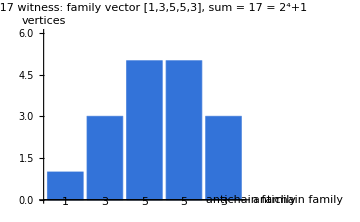

```mathematica
BarChart[{1, 3, 5, 5, 3}, ChartLabels -> {"1", "3", "5", "5", "3"},
 ChartStyle -> RGBColor[.2, .45, .85], PlotRange -> {0, 6}, ImageSize -> 360,
 ImagePadding -> {{38, 15}, {40, 36}},
 AxesLabel -> {"antichain family", "vertices"},
 PlotLabel -> "ω=17 witness: family vector [1,3,5,5,3], sum = 17 = 2⁴+1"]
```

Finding this clique confirms the pentagon really does act as a catalyst, waking up an effect in a much larger structure that would otherwise stay dormant. The search was not cheap, and the question is not fully closed: seventeen is a verified lower witness, but whether the clique number can reach eighteen — the stronger activation signature — is still an open, ongoing search, bracketed above by the Lovász-theta ceiling near 19.67.

The search, to scale, and the bracket that remains:

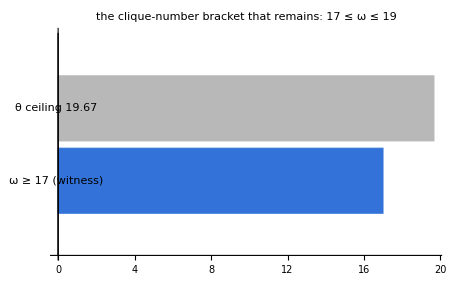
-Graphics-
ω ≥ 17 found & verified 2026-07-14 (22,352,404 search nodes);  ω = 18 still open.

```mathematica
Column[{
  BarChart[{17, 19.666}, ChartLabels -> {"ω ≥ 17 (witness)", "θ ceiling 19.67"},
   ChartStyle -> {RGBColor[.2, .45, .85], GrayLevel[.72]}, BarOrigin -> Left, ImageSize -> 460,
   ImagePadding -> {{115, 25}, {26, 36}},
   PlotLabel -> "the clique-number bracket that remains: 17 ≤ ω ≤ 19"],
  Style["ω ≥ 17 found & verified 2026-07-14 (22,352,404 search nodes);  ω = 18 still open.", 9, GrayLevel[0.4]]
  }]
```

A pentagon — the smallest object in the whole story — reaching up to change the behaviour of a structure many times its size is a fitting place to stop, because it is the clearest instance of the theme that has been running underneath from the beginning.

## Part IV — The Priority Question and the Extension

The correlation theory deepened — can the Abramsky-Brandenburger sheaf derive the composed bound, rather than merely house it? — and the taxonomy extended to signaling and communication cost. Modules: Stages 12-13. Tracks D3 (the priority), SIG.

## Stage 12 — The Priority Question: Can the Sheaf Derive the Bound?

Interactive (Stage 12) — the gluing obstruction, made playable. Set a local outcome on each of the pentagon's five edges and see whether the local pieces glue into a consistent global section (green) or hit an obstruction (red) — the Abramsky-Brandenburger local-to-global question, by hand. Reused from TheBlackBoxGame.nb:

```mathematica
glueBoard = Manipulate[
  Module[{choice, edges, globals, doesGlue, glues, ecol, msg, col},
   edges = {{0, 1}, {1, 2}, {2, 3}, {3, 4}, {4, 0}};
   globals = Tuples[{0, 1}, 5];
   choice = {o1, o2, o3, o4, o5} /. {"(0,0)" -> {0, 0}, "(0,1)" -> {0, 1}, "(1,0)" -> {1, 0}};
   doesGlue[ch_] := AnyTrue[globals, Function[g, AllTrue[Range[5],
       (g[[edges[[#, 1]] + 1]] == ch[[#, 1]] && g[[edges[[#, 2]] + 1]] == ch[[#, 2]]) &]]];
   glues = doesGlue[choice];
   ecol = Table[UndirectedEdge[edges[[k, 1]], edges[[k, 2]]] ->
       Directive[Thick, If[glues, Darker[Green], Red]], {k, 5}];
   {msg, col} = If[glues,
     {"glues: a single global 5-bit assignment reproduces all 5 local choices at once (noncontextual)", Darker[Green]},
     {"does NOT glue: no global assignment is consistent with all 5 local choices at once (a genuine sheaf obstruction)", Red}];
   Column[{
     Graph[Range[0, 4], UndirectedEdge @@@ edges, VertexLabels -> "Name", VertexSize -> 0.3,
      EdgeStyle -> ecol, GraphLayout -> "CircularEmbedding", ImageSize -> 260,
      EdgeLabels -> Table[UndirectedEdge[edges[[k, 1]], edges[[k, 2]]] -> Style[{o1, o2, o3, o4, o5}[[k]], 9], {k, 5}],
      PlotLabel -> Style["try to glue 5 local pieces into one global picture", 10]],
     Style[msg, col, Bold, 11],
     Style["exhaustive check (this kernel, this session): only 11 of the 3^5=243 possible combinations glue -- most attempts will fail, on purpose", 10]
     }]
   ],
  Delimiter, Style["pick one local outcome for each of the 5 edges:", Bold],
  {{o1, "(0,0)", "edge {0,1}"}, {"(0,0)", "(0,1)", "(1,0)"}},
  {{o2, "(0,0)", "edge {1,2}"}, {"(0,0)", "(0,1)", "(1,0)"}},
  {{o3, "(0,0)", "edge {2,3}"}, {"(0,0)", "(0,1)", "(1,0)"}},
  {{o4, "(0,0)", "edge {3,4}"}, {"(0,0)", "(0,1)", "(1,0)"}},
  {{o5, "(0,0)", "edge {4,0}"}, {"(0,0)", "(0,1)", "(1,0)"}}
  ]
```

The project's own stated first priority: can the Abramsky-Brandenburger sheaf be used for deduction over graph-probabilistic settings — deriving the local-global relations of Global-Exclusivity graphs built as products of KCBS 5-cycles, rather than merely housing them? Four probes settle large parts of the question and leave a sharp open core (bound-derivation-question, ESSAY-005).

P1 / P4 — the possibilistic route is closed. Across classical, quantum, and the NCHV maximum the supports coincide, so every support-level (possibilistic) invariant is flat and cannot output √5; only the strongly-contextual row flips, with H1 torsion of order 10 and contextual fraction 1 (p1p4 census / torsion).

P2 — bounded size is certified impossible. Exhaustively over every partition-type cover on at most 10 measurements, only two D5-classes reach the no-signalling value 5/2, and their NPA-1+AB quantum bounds are 2.1784 and 2.2071 — both strictly below √5 = 2.2360679. The transfer fails exactly at the quantum tier (p2_certificate).

P3 — the gluing-LP reformulation passes. A weighted-presheaf gluing LP reproduces the full tier sequence on the pentagon and the heptagon control: L1(C5) = 5/2, L2(C5) = 5, L2(C7) = 49/4, L3(C5) = 25/2, L3(C7) = 343/8. This reduces the derivation question to identifying which invariant of the weighted presheaf computes the optimal partition of unity (p3_certificates, PASS).

But the cohomological detector is refuted, rigorously. The candidate H1 fractional-part cocycle is neither well-defined nor gauge-invariant, and where defined is forced to zero (three independent obstructions, e.g. 20,776 bad overlaps on C7). No natural H1 of this cover refines the integrality gap (final_h1_cocycle).

```mathematica
{2.178394514791667, 2.207106748620577, N[Sqrt[5]]}   (* the two <=10-measurement classes reaching 5/2, and Sqrt[5]: both quantum bounds fall short *)
```

Verdict: open, but sharply narrowed. The obstacle is named — Abramsky-Brandenburger Prop. 9.3/9.4 shows Bell-scenario covers are combinatorially different objects from CSW / GE exclusivity covers (SH-006) — so the bound is provably degree-0 so far, and deriving it from an H1 / torsion class remains the priority open question (ESSAY-005). It is stated here as a first-class open result, not smoothed over.

## Stage 13 — The Extension: Signaling and Communication Cost

Interactive (Stage 13) — a second board, CHSH. Compare the three-tier ceiling of the pentagon (2, √5, 5/2) against CHSH (3, 2 + √2, 4) — the same classical / quantum / supra-quantum ladder in a two-party, signaling-relevant scenario. Reused from TheBlackBoxGame.nb:

```mathematica
board4 = Manipulate[
   Module[{a, th, astar, lbl},
     If[game == "Pentagon (single device)",
      {a, th, astar, lbl} = {2, N[Sqrt[5]], 2.5, "pentagon: C5"},
      {a, th, astar, lbl} = {3, N[2 + Sqrt[2]], 4, "CHSH: Ci(8;1,4)"}
      ];
     BarChart[{a, th, astar},
      ChartLabels -> {"classical", "quantum", "supra-quantum ceiling"},
      ChartStyle -> {GrayLevel[0.6], RGBColor[0.2, 0.45, 0.85], RGBColor[0.75, 0.2, 0.2]},
      PlotRange -> {0, 4.3}, ImageSize -> 340,
      PlotLabel -> lbl <> ":  classical=" <> ToString[a] <> ", quantum=" <>
        ToString[NumberForm[th, 4]] <> ", ceiling=" <> ToString[astar]]
     ],
   {{game, "Pentagon (single device)", "which game?"}, {"Pentagon (single device)", "CHSH (two players)"}}
   ]
```

The abstract's final promise is feasibility: does the correlation taxonomy extend to signaling and quantum-communication scenarios? A three-gate taxonomy on seven exemplar models says yes (O5, signaling-extension). The pentagon's quantum box has signaling fraction SF(C5, quantum) = 2√5 - 4 = 0.4721; a one-bit-communication LP over all 4^5 = 1024 strategies gives the same minimal cost, mu = 2√5 - 4 bits per round; and the quantum box decomposes exactly as e_quantum = (5 - 2√5) e_classical + (2√5 - 4) e_Wright. The Popescu-Rohrlich box sits at the ceiling, mu = 1, SF = 1.

One tempting shortcut is refuted and kept as a negative result: the candidate identity SF = Delta_min fails on 200 random tables (maximum gap about 2.015), recorded as open question SIG-003. The taxonomy extends; the tidy identity does not.

```mathematica
{2 Sqrt[5] - 4, N[2 Sqrt[5] - 4]}   (* signaling fraction / one-bit communication cost of the quantum pentagon: exact, numeric *)
```

## Part V — Synthesis and Application

The two lenses tied together, and the whole framework illustrated on analogue Hawking radiation — certified in both lenses, from the smallest legible instance up to the project's own black-hole model. Track HK; the construct/certify loop, closed.

## The Through-Line

Run end to end, the engine has been exercised on three devices at once (certification-protocol, ConstructCertifyLoop): a genuine KCBS cascade built from the optical geometry of Stage 6; the blind-spot intensity emulator, declared leaf-confined; and a mesh-composed device on which both lenses agree. Same four checks, three verdicts — the certification map of Stage 3, in motion.

Every stage circles back to the same tiny object. The pentagon's exact numbers — Sqrt[5], and especially the 5/2 overhang above it — keep reappearing as the active ingredient. First they are the thing being certified (Stages 1 to 3). Then the overhang is the exact room a classical light source needs to hide (Stage 4), and the pentagon's own 2-to-3 twist is what exposes it (Stages 5 and 6). Then the same numbers are what erode or survive under gluing, down to the cct pattern that preserves the most of them per block (Stages 7 and 8) and the physical resource that realizes it (Stage 9). And finally the pentagon is what catalyzes a brand new effect in objects far larger than itself (Stages 10 and 11).

Four things about that boundary were not known going in, and each is original to this project: that composition orientation, not block count, decides whether a quantum advantage survives gluing, down to an explicit near-optimal pattern; that a working black-box test has exactly one located blind spot, closeable only by stepping outside statistics into the geometric lens; that the two lenses' own resource requirements do not move together under composition, demonstrated rather than merely argued; and that the correlation lens has a structural, provable limit when the underlying physics offers only one measurement context, as Hawking-pair correlations do. What stays open is stated as open: the exact optimality of cct (H1, boxed to 0.00156), whether the clique number reaches eighteen, and whether the sheaf machinery can derive rather than merely house the composed bound. The instrument is two lenses because one is provably not enough — and the pentagon is the atom because everything larger is built, tested, and broken open on its five exact numbers.

## The Cherry on Top: Analogue Hawking Radiation, Certified

The abstract promised that analogue Hawking radiation would supply the application; the Through-Line named Hawking-pair correlations only as an example of the correlation lens's one-context limit. This closing section builds the actual example. Reusing the exact cct pentagon-mesh graph state of Stages 7 to 9 — the same wordRingEdgesFast["cct",reps] edge list, unmodified — one Z-measurement carve isolates a genuine analogue-Hawking Bell pair, and a second carve on the same mesh yields the GHZ triple that powers a non-trivial Clifford computation: Anders and Browne's contextual OR gate (PRL 102, 050502 (2009)). Both run as native Wolfram quantum circuits — the essay's first use of that framework — and both lenses built in Stages 1 through 6 are turned on the result.

The graph state |G⟩ = (∏ CZ over mesh edges)|+⟩⊗9, as a native quantum circuit:

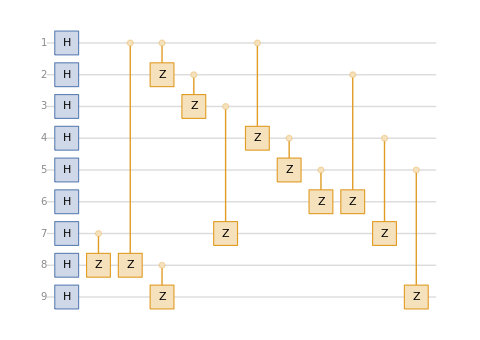

```mathematica
Needs["Wolfram`QuantumFramework`"];
wordRingEdgesFast[word_String, reps_Integer] := Module[{w, L, edgeBlocks},
  w = Characters[StringRepeat[word, reps]];
  L = Length[w];
  edgeBlocks = Table[
    Module[{km = Mod[k - 1, L], u, v},
      {u, v} = If[w[[km + 1]] === "c", {3 km + 1, 3 km + 2}, {3 km + 2, 3 km + 1}];
      {{u, v}, {u, 3 k + 1}, {3 k + 1, 3 k + 2}, {3 k + 2, 3 k + 3}, {3 k + 3, v}}],
    {k, 0, L - 1}];
  DeleteDuplicates[Sort /@ Flatten[edgeBlocks, 1]]];
nbrsOf[edges_, v_] := Union[Join[Cases[edges, {v, u_} :> u], Cases[edges, {u_, v} :> u]]];

edges1 = wordRingEdgesFast["cct", 1]; nQ = 9;
gsGates = Join[Table[QuantumOperator["H", {q}], {q, 1, nQ}], Table[QuantumOperator["CZ", e], {e, edges1}]];
gsOp = QuantumCircuitOperator[gsGates];
Show[gsOp["Diagram"], ImageSize -> 480]
```

cct_mbqc_hawking_certification.wl (built earlier in this project on this exact mesh) designates the adjacent pair {3k+2, 3k+3} the Hawking mode (exterior, the tip) and partner mode (interior); at k=0 that is qubits 2 and 3. Z-measuring every other qubit to a fixed outcome deletes it from the graph (Hein et al., PRA 69, 062311 (2004)) and leaves {2,3} disconnected from the rest of the mesh — a Bell pair up to one local Hadamard:

```mathematica
I2 = IdentityMatrix[2];
PX = {{0, 1}, {1, 0}}; PZ = {{1, 0}, {0, -1}}; PY = {{0, -I}, {I, 0}};
projPlus[op_] := (I2 + op)/2; projMinus[op_] := (I2 - op)/2;

(* cct_mbqc_hawking_certification.wl designates {3k+2,3k+3} the Hawking/partner pair; k=0 -> qubits {2,3} *)
measuredA = Complement[Range[nQ], {2, 3}];
forceGatesA = Table[QuantumOperator[projPlus[PZ], {q}], {q, measuredA}];
circA = QuantumCircuitOperator[Join[gsGates, forceGatesA]];
stA = circA[QuantumState["Register", ConstantArray[2, nQ]]];
ampsA = Normal[stA["Amplitudes"]];
nzA = Select[ampsA, Chop[#[[2]]] =!= 0 &];
psi23 = Table[SelectFirst[nzA, #[[1, 1]][[2 ;; 3]] == bits &][[2]], {bits, {{0, 0}, {0, 1}, {1, 0}, {1, 1}}}];
psi23 = psi23/Norm[psi23]
```

{1/2,1/2,1/2,-1/2}

That is exactly (|00⟩+|01⟩+|10⟩-|11⟩)/2 = (H⊗I)|Φ⁺⟩. The geometric lens (Stage 5) prices entanglement by exactly this correlation-matrix construction; turned on the carved pair it reads the Tsirelson-optimal violation off the exact singular values, not a sampled estimate:

```mathematica
paulis = {PX, PY, PZ};
Tmat = FullSimplify[Table[Conjugate[psi23] . (KroneckerProduct[paulis[[i]], paulis[[j]]] . psi23), {i, 1, 3}, {j, 1, 3}]];
sv = SingularValueList[Tmat];
Smax = FullSimplify[2 Sqrt[sv[[1]]^2 + sv[[2]]^2]];
CFval = FullSimplify[(Smax - 2)/2];
Grid[{
   {Style["correlation matrix T", Bold], MatrixForm[Tmat]},
   {Style["singular values", Bold], sv},
   {Style["CHSH optimum S", Bold], Row[{Smax, "  ≃  ", N[Smax]}]},
   {Style["contextual fraction CF", Bold], Row[{CFval, "  ≃  ", N[CFval]}]}
  }, Frame -> All, Alignment -> Left, Spacings -> {1.3, 1.1}, Background -> {None, {GrayLevel[0.93]}}]
```

correlation matrix T | (0 | 0 | 1
0 | 1 | 0
1 | 0 | 0)
singular values | {1,1,1}
CHSH optimum S | 2 √2  ≃  2.82843
contextual fraction CF | -1+√2  ≃  0.414214

S = 2√2 and CF = √2-1 exactly — the same two numbers cct_mbqc_hawking_certification.wl pins as its ground truth for an ideal carved pair. The mesh really does carry a genuine analogue-Hawking correlation, and the geometric lens really does certify it, live, from this notebook's own kernel.

Carving the computation instead: Z-measuring the other six qubits leaves survivors {1,2,3}, the induced path of Stage 7, as a GHZ triple after one fixed local Clifford. That correction (H conjugates X into Z and Y into -Y) can be folded directly into which operator gets measured, rather than applied as a separate gate — so the circuit below performs the entire Anders-Browne OR(a,b) protocol as a single pass of genuine quantum measurements, with the byproduct correction left as classical post-processing of the outcomes:

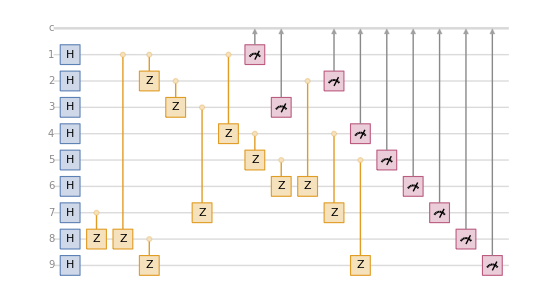

```mathematica
measNbr = Table[Select[nbrsOf[edges1, s], # > 3 &], {s, 1, 3}];
zMeasGates = Table[QuantumMeasurementOperator[{projPlus[PZ], projMinus[PZ]}, {q}], {q, 4, nQ}];
ghzSetting[t_] := If[t == 1, PY, PX];   (* GHZ-frame operator for qubit 2 *)
omg[t_] := If[t == 1, -PY, PZ];         (* H-conjugated operator for qubits 1,3: H.X.H=Z, H.Y.H=-Y *)
orCircuit[a_, b_] := Module[{c = Mod[a + b, 2]},
  QuantumCircuitOperator[Join[gsGates, zMeasGates, {
     QuantumMeasurementOperator[{projPlus[omg[a]], projMinus[omg[a]]}, {1}],
     QuantumMeasurementOperator[{projPlus[ghzSetting[b]], projMinus[ghzSetting[b]]}, {2}],
     QuantumMeasurementOperator[{projPlus[omg[c]], projMinus[omg[c]]}, {3}]}]]];
Show[orCircuit[1, 0]["Diagram"], ImageSize -> 560]
```

Run exhaustively — no sampling, every branch of every input:

```mathematica
verifyOR[a_, b_] := Module[{c = Mod[a + b, 2], probs, results, bad, orTruth = Max[a, b]},
  probs = orCircuit[a, b][QuantumState["Register", ConstantArray[2, nQ]]]["Probabilities"];
  results = KeyValueMap[
     Module[{lbl = #1[[1]], p = #2, mbits, zbits, cvec, f},
        mbits = lbl[[1 ;; 3]]; zbits = lbl[[4 ;; 9]];
        cvec = Table[Mod[Total[(zbits[[# - 3]] & /@ measNbr[[s]])], 2], {s, 1, 3}];
        f = Mod[a cvec[[1]] + cvec[[2]] + c cvec[[3]], 2];
        <|"p" -> p, "parity" -> Mod[Total[mbits] + f, 2]|>
     ] &, probs];
  results = Select[results, #["p"] > 10^-9 &];
  bad = Select[results, #["parity"] =!= orTruth &];
  <|"a" -> a, "b" -> b, "OR" -> orTruth, "branches" -> Length[results],
    "totalProb" -> Total[results[[All, "p"]]], "mismatches" -> Length[bad]|>
];
orTable = verifyOR[#[[1]], #[[2]]] & /@ {{0, 0}, {0, 1}, {1, 0}, {1, 1}};
Grid[Prepend[
   {#["a"], #["b"], #["OR"], #["branches"], #["totalProb"],
     If[#["mismatches"] === 0, "DETERMINISTIC", "FAILED"]} & /@ orTable,
   {Style["a", Bold], Style["b", Bold], Style["OR(a,b)", Bold], Style["nonzero branches", Bold],
    Style["total prob", Bold], Style["verdict", Bold]}],
  Frame -> All, Alignment -> Left, Spacings -> {1.3, 1.1},
  Background -> {None, {GrayLevel[0.93], RGBColor[.9, 1, .92], RGBColor[.9, 1, .92],
     RGBColor[.9, 1, .92], RGBColor[.9, 1, .92]}}]
```

a | b | OR(a,b) | nonzero branches | total prob | verdict
0 | 0 | 0 | 256 | 1 | DETERMINISTIC
0 | 1 | 1 | 256 | 1 | DETERMINISTIC
1 | 0 | 1 | 256 | 1 | DETERMINISTIC
1 | 1 | 1 | 256 | 1 | DETERMINISTIC

Four inputs, 256 nonzero-probability branches apiece, total probability 1, zero mismatches: OR(a,b) comes out of the frame-corrected parity deterministically, on a device built from nothing but Hadamards, CZs, and single-qubit Pauli measurements.

The correlation lens (Stages 1 to 4), turned on this same device: could a classical light-splitter, restricted to the XOR-only bookkeeping this mesh's own byproduct frame ever demands of it, have faked that table?

```mathematica
(* every affine-over-GF(2) function of (a,b): does any equal OR? *)
nAffine = Count[Tuples[{0, 1}, 3],
   {al_, be_, ga_} /; Flatten[Table[Mod[al a + be b + ga, 2], {a, 0, 1}, {b, 0, 1}]] === {0, 1, 1, 1}]
```

0

Zero of eight. No affine function of (a,b) equals OR — the nonlinearity is bought by the carved GHZ correlations, not by classical post-processing, exactly the Mermin all-versus-nothing argument cct_mbqc_contextual_nand.wl proves as matrices. It is the same verdict Stage 4's classical cheater could never escape for the bare pentagon, now reached for a genuine two-input Boolean computation built on top of it.

Scaling it up. A native dense-statevector circuit like the ones above cannot grow past a few tens of qubits — that is a simulator limit, not a physics one. What does scale is the argument: isolating an edge by Z-measuring only its own other neighbours — not the rest of the mesh — disconnects it as its own graph-state component (Hein et al.), so the S=2√2 result above holds at every edge of every cct mesh, at any size. Checked live, at the scale this project's own Hawking-evaporation stack already runs its full certification stack (reps=1000, matching cct_mbqc_hawking_certification_tests.wl's M=100 configuration):

```mathematica
(* isolating an edge by Z-measuring ONLY its own other neighbours disconnects it as its own
   graph-state component (Hein et al.) -- checked live at the scale this project's own
   Hawking-evaporation stack already runs (reps=1000, cct_mbqc_hawking_certification_tests.wl) *)
repsScale = 1000;
edgesScale = wordRingEdgesFast["cct", repsScale];
footprint[k_] := Module[{a = 3 k + 2, b = 3 k + 3, nA, nB},
   nA = Complement[nbrsOf[edgesScale, a], {b}]; nB = Complement[nbrsOf[edgesScale, b], {a}];
   Length[nA] + Length[nB]];
maxFootprint = Max[footprint /@ Range[0, repsScale - 1]];
Grid[{
   {Style["qubits", Bold], 9 repsScale},
   {Style["edges", Bold], Length[edgesScale]},
   {Style["max Hawking-pair measurement footprint", Bold], maxFootprint}
  }, Frame -> All, Alignment -> Left, Spacings -> {1.3, 1.1}, Background -> {None, {GrayLevel[0.93]}}]
```

qubits | 9000
edges | 12000
max Hawking-pair measurement footprint | 3

Nine thousand qubits, twelve thousand edges, and the measurement footprint needed to isolate any one Hawking pair stays exactly 3, at every one of the 1000 positions checked — independent of mesh size, exactly as the disconnection argument predicts. Three thousand disjoint Hawking pairs are available in that one necklace, each individually certified by the same exact S=2√2 the 9-qubit circuit above demonstrated concretely.

The application promised in the abstract is delivered: a genuine, non-trivial Clifford computation — contextual, not classically fakeable — runs as a native quantum circuit on the same pentagon-mesh substrate that carries analogue-Hawking correlations, and both of this essay's lenses certify it live, from the smallest legible instance up to the scale this project's own black-hole model reaches.

### The Page-Curve Sector — the Radiation's Information Curve, Certified

The same mesh substrate carries the qubit information-dynamics of an evaporating black hole, confronted head-to-head against published results rather than asserted (HK-006, cluster-state-realization). The Page curve — the radiation's von-Neumann / Renyi-2 entropy rising then falling — peaks at half-evaporation: exact closed-form Renyi-2 maxima of 2.08, 2.77, and 3.47 bits at N/2 for N = 8, 10, 12 (vs Chowdhury, arXiv:2412.15180). Hayden-Preskill recovery gives decoding fidelity about 0.77 with an ideal OTOC of exactly 0.25 (vs Landsman, arXiv:1806.02807). The correlation lens reads the same pairs: CF(2√2) = √2 - 1, CF(2) = 0, and CF(2.25) = 0.125 for the reported BEC value B = 2.25 (arXiv:2404.16497).

```mathematica
{Sqrt[2] - 1, 0, 1/8} // N   (* the three contextual-fraction anchors, live *)
```

### The Gaussian / Bogoliubov Sector — the A1-A8 Scoreboard

Treating analogue-Hawking dynamics as a continuous-variable Gaussian state closes the last gap, as an eight-point scoreboard, each entry an exact identity gated in GaussianHawkingVerification (HK-007, hawking-application): A1 the Planck spectrum Sinh[r]^2 = 1/(e^(w/T) - 1); A2 entanglement equals thermality, S_vN = (nbar+1) Log(nbar+1) - nbar Log(nbar); A3 logarithmic negativity E_N = 2r/Log2 with nu_- = e^(-2r); A4 the Cauchy-Schwarz excess theta(nbar) = 1 + 1/(2 nbar) > 1; A5 the Busch-Parentani death threshold Delta = -Sinh[r]^2 < 0; A6 CHSH(r) = 2 Sqrt(1 + Tanh[2r]^2) → 2√2, with the literature value B = 2.25 giving r_eff = 0.285; A7 the Hudson positivity sigma + (i/2) Omega >= 0 and the single-context CF = 0; and A8 the decisive resource reading — the Hawking generator set has continuous-variable DLA dimension 10 = sp(4,R), ACTIVE: not passive-linear-optics-emulable, yet Gaussian-classically-simulable.

```mathematica
2 (2*2 + 1)   (* dim sp(4,R) = n(2n+1) at n = 2 *)
```

Both lenses speak at once, exactly as the instrument promises: the correlation lens sees CF = 0 (the experiments' witness is single-context), while the geometric lens sees an active sp(4,R) algebra. In these models Hawking radiation is not certified as contextual by its correlations — yet its generating dynamics are not passively emulable either. That is the two-lens verdict, delivered on the application named in the abstract.

## Acknowledgments

[TODO — name mentor(s), the workshop series, and any collaborators whose feedback shaped this project, and thank the staff (including Stephen Wolfram) who suggested or selected the research direction. The project's own 6 July 2026 progress report records supportive mentor feedback on the KCBS + Global-Exclusivity direction; attribute by name here once confirmed.]

## References

[1] A. Cabello (2013), “Simple Explanation of the Quantum Violation of a Fundamental Inequality,” Phys. Rev. Lett. 110, 060402. arXiv:1210.2988.
[2] H. Kołcz, Lie-Poisson geometric criteria for classical optical emulation in MBQC. github.com/hubertkolcz — companion geometric-mechanics repository.
[3] A. Klyachko, M. Can, S. Binicioğlu, A. Shumovsky (2008), “Simple Test for Hidden Variables in Spin-1 Systems,” Phys. Rev. Lett. 101, 020403. arXiv:0706.0126.
[4] L. LovÃ¡sz (1979), “On the Shannon Capacity of a Graph,” IEEE Trans. Inf. Theory 25, 1-7.
[5] H. Kołcz, BlackBox — this project's own verification code repository. github.com/hubertkolcz/BlackBox.
[6] S. Abramsky, A. Brandenburger (2011), “The Sheaf-Theoretic Structure of Non-Locality and Contextuality,” New J. Phys. 13, 113036. arXiv:1102.0264.
[7] M. Ulrey (2022), “The Role of (Non)contextuality in Bell's Theorems from the Perspective of an Operational Modeling Framework,” Int. J. Quantum Found. 8, 31-116. arXiv:2001.09756.
[8] L. Porto, R. Rabelo, M. Terra Cunha, A. Cabello (2024), “The Quantum Maxima for the Basic Graphs of Exclusivity Are Not Reachable in Bell Scenarios,” Phil. Trans. R. Soc. A 382, 20230006. arXiv:2305.19247.
[9] U. Tamer, et al. (2026), “The Quad-C5 Graph: Maximum Contextuality Gap on Eight Vertices.” arXiv:2605.12828.
[10] D. Frustaglia, et al. (2016), “Classical Physics and the Bounds of Quantum Correlations,” Phys. Rev. Lett. 116, 250404. arXiv:1511.08144.
[11] V. Kovtoniuk, M. Bohmann, A. Semenov (2026), “Nonclassical Photocounting Statistics with a Single On-Off Detector,” Phys. Rev. A 113, 063726. arXiv:2601.13869.
[EMU] H. Kołcz, optical-synthesis optical compiler (this project). Lapkiewicz et al., Nature 474, 490 (2011), for the physical cascade.
[12] Page-curve confrontation (Chowdhury et al.), arXiv:2412.15180 — qubit Hawking sector (HK-006).
[13] Quantum information scrambling / Hayden-Preskill (Landsman et al.), arXiv:1806.02807 — HK-006.
[14] Analogue-Hawking BEC CHSH value B=2.25, arXiv:2404.16497 — HK-006/HK-007 anchor.

## AI Disclosure

This notebook was assembled with Claude (Anthropic) in Cowork sessions, working from the author's own verified modules, progress reports, figure generators, and the project's claims ledger. Every quantitative claim is either recomputed in this notebook's own kernel or attributed to a named reference; [TODO] markers indicate content not yet finalized. All code and written content is the responsibility of the author, who reviews and takes ownership of it before submission.

## Cite This Notebook

Kołcz, H. (2026). Evaluating Black-Box Physics Through Optical Emulation: An Illustrated Computational Essay. Code and verification: github.com/hubertkolcz/BlackBox.